```mathematica
Exit[];
```

```mathematica
$HistoryLength=3;
SetDirectory[NotebookDirectory[]];
SetOptions[ListLinePlot,{ImageSize->Large,BaseStyle->FontSize->15,AxesStyle->Black}];
SetOptions[Plot,{ImageSize->Large,BaseStyle->FontSize->15, AxesStyle->Black}];
SetOptions[ListPlot,{ImageSize->Large,BaseStyle->FontSize->15,AxesStyle->Black}];
SetOptions[ListLogPlot,{ImageSize->Large,BaseStyle->FontSize->15, AxesStyle->Black}];
```

## Theoretical part

### Initial parameters

```mathematica
μ0= 4Pi 10^-7;
(*1 magnet*)
r1[x_,y_, z_]:={x,y, z};
m1[θ1_,ϕ_, p_ ]:=p{Sin[ϕ]Cos[θ1],Sin[ϕ]Sin[θ1], Cos[ϕ]};
(*2 magnet*)
r2[x_,y_, z_]:={x,y, z};
m2[θ1_,ϕ_, p_ ]:=p{Sin[ϕ]Cos[θ1],Sin[ϕ]Sin[θ1], Cos[ϕ]};
M = 16.7 10^-3;
g=9.81;
```

```mathematica
ℛ=ImplicitRegion[√(x^2+y^2)>=0.00884&&Abs[x]<=0.05&&Abs[y]<=0.05,{x,y}];
```

### Field

```mathematica
Field[x_, y_,z_, θ1_, ϕ1_, p1_]:=μ0/(4 π) ((3m1[θ1, ϕ1, p1].r2[x, y, z])/Norm[r2[x, y, z]]^5 r2[x, y, z]-m1[θ1, ϕ1, p1]/Norm[r2[x, y, z]]^3)
```

```mathematica
Field[x, 0,z,0,Pi/2,  2.07]
```

{((3 x (0.+2.07 x))/((Abs[x]^2+Abs[z]^2)^(5/2))-2.07/((Abs[x]^2+Abs[z]^2)^(3/2)))/10000000,0.,(0.+(3 (0.+2.07 x) z)/((Abs[x]^2+Abs[z]^2)^(5/2)))/10000000}

```mathematica
Manipulate[
Show[
StreamPlot[Field[x, 0,z,ϕ,Pi/2,  2.07][[1;;3;;2]] ,{x, -0.05, 0.05},  {z, -0.05, 0.05}, ImageSize->Medium, FrameLabel->{"x", "z"},PlotLegends->Automatic,RegionBoundaryStyle->None,RegionFillingStyle->None, StreamColorFunction->"Rainbow", PlotLegends->BarLegend[{Automatic,{0, 0.015}}, 60], PlotRange-> {{-0.05, 0.05}, {-0.05, 0.05}, {0, 0.015}}], 
Graphics[
{
{Arrowheads[Large], Darker[Red], Arrow[{8 10^-3{-Sin[ Pi/2], -Cos[ Pi/2]}, 8 10^-3{Sin[  Pi/2], Cos[ Pi/2]}}]}
}
]
], {ϕ, 0, 2Pi}
]
```

General::prng: Value of option PlotRange -> {{-0.05,0.05},{-0.05,0.05},{0,0.015}} is not All, Full, Automatic, a positive machine number, or an appropriate list of range specifications.

```mathematica
{min,max}={0,0.1};
sf=Log[#/min]/Log[max/min]&;
isf=InverseFunction@sf;
```

```mathematica
Manipulate[
Show[
StreamPlot[
Field[x, 0,z,ϕ,Pi/2,  2.07][[1;;3;;2]] ,
{x, -0.05, 0.05},  {z, -0.05, 0.05},
 ImageSize->Medium, FrameLabel->{"x", "z"},StreamColorFunctionScaling->False]
], {ϕ, 0, 2Pi}
]
```

```mathematica
Manipulate[
StreamPlot[
Field[x,0,z,ϕ,Pi/2,2.07][[1;;3;;2]],{x,-0.05,0.05},{z,-0.05,0.05},
ImageSize->Medium,FrameLabel->{"x","z"},
StreamColorFunction->Function[{x,z,vx,vz,n},If[vz>0,Red,Black]],StreamColorFunctionScaling->False],
{{ϕ,0},0,2 Pi,0.01,Appearance->"Labeled"},TrackedSymbols:>{ϕ}]
```

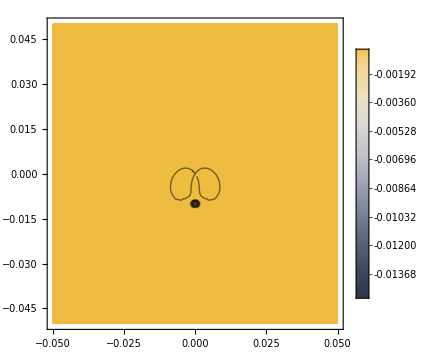

```mathematica
ContourPlot[
Norm[Field[x,0,z,0,Pi/2,2.07]]-Norm[Field[x,0,z,0,Pi/2,2.07]+Field[x,0,z+0.01,0,Pi/2,0.19]],{x,-0.05,0.05},{z,-0.05,0.05},
ImageSize->Medium, PlotRange->All,  ColorFunction->"GrayYellowTones",PlotLegends->BarLegend[{Automatic,{-0.015, 0}}, 60], PlotRange-> {-0.015, 0}, ClippingStyle->Automatic
]
```

### Forces

```mathematica
Force[x_, y_,z_, θ1_, ϕ1_, θ2_, ϕ2_, p1_, p2_]:=(3 μ0)/(4 π Norm[r2[x, y, z]]^5) ((m1[θ1, ϕ1, p1].r2[x, y, z])*m2[θ2, ϕ2, p2]+(m2[θ2, ϕ2, p2].r2[x, y, z])*m1[θ1, ϕ1, p1]+(m1[θ1, ϕ1, p1].m2[θ2, ϕ2, p2])*r2[x, y, z]-(5 (m1[θ1, ϕ1, p1].r2[x, y, z])(m2[θ2, ϕ2, p2].r2[x, y, z]))/Norm[r2[x, y, z]]^2 r2[x, y, z])
```

```mathematica
Force[x, y,-0.005,θ1 ,  -(90-24.5)/180 Pi+Pi, 0, 0, 2.07 , 0.19][[2]]x-Force[x, y,-0.005, θ1,  -(90-24.5)/180 Pi+Pi, 0, 0, 2.07 , 0.19][[1]] y
```

-(3 y (0.-0.163099 x-0.00178944 Cos[θ1]+(0.00475 x (0.00429208+1.88362 x Cos[θ1]+1.88362 y Sin[θ1]))/(0.000025+Abs[x]^2+Abs[y]^2)))/(10000000 (0.000025+Abs[x]^2+Abs[y]^2)^(5/2))+(3 x (0.-0.163099 y-0.00178944 Sin[θ1]+(0.00475 y (0.00429208+1.88362 x Cos[θ1]+1.88362 y Sin[θ1]))/(0.000025+Abs[x]^2+Abs[y]^2)))/(10000000 (0.000025+Abs[x]^2+Abs[y]^2)^(5/2))

```mathematica
Simplify[%267]
```

```mathematica
(1.3420791293840415*^-14 y Cos[θ1]-1.3420791293840415*^-14 x Sin[θ1]+Abs[x]^2 (5.368316517536166*^-10 y Cos[θ1]-5.368316517536166*^-10 x Sin[θ1])+Abs[y]^2 (5.368316517536166*^-10 y Cos[θ1]-5.368316517536166*^-10 x Sin[θ1]))
```

1.34208×10^-14 y Cos[θ1]-1.34208×10^-14 x Sin[θ1]+Abs[x]^2 (5.36832×10^-10 y Cos[θ1]-5.36832×10^-10 x Sin[θ1])+Abs[y]^2 (5.36832×10^-10 y Cos[θ1]-5.36832×10^-10 x Sin[θ1])

```mathematica
TrigReduce[1.3420791293840415*^-14 y Cos[θ1]-1.3420791293840415*^-14 x Sin[θ1]+Abs[x]^2 (5.368316517536166*^-10 y Cos[θ1]-5.368316517536166*^-10 x Sin[θ1])+Abs[y]^2 (5.368316517536166*^-10 y Cos[θ1]-5.368316517536166*^-10 x Sin[θ1])]
```

```mathematica
1.3420791293840415*^-14 y Cos[θ1]+5.368316517536166*^-10 y x^2 Cos[θ1]+5.368316517536166*^-10 y y^2 Cos[θ1]-1.3420791293840414*^-14 x Sin[θ1]-5.368316517536166*^-10 x x^2 Sin[θ1]-5.368316517536166*^-10 x y^2 Sin[θ1]
```

1.34208×10^-14 y Cos[θ1]+5.36832×10^-10 x^2 y Cos[θ1]+5.36832×10^-10 y^3 Cos[θ1]-1.34208×10^-14 x Sin[θ1]-5.36832×10^-10 x^3 Sin[θ1]-5.36832×10^-10 x y^2 Sin[θ1]

```mathematica
Simplify[1.3420791293840415*^-14 y Cos[θ1]+5.368316517536166*^-10 x^2 y Cos[θ1]+5.368316517536166*^-10 y^3 Cos[θ1]-1.3420791293840414*^-14 x Sin[θ1]-5.368316517536166*^-10 x^3 Sin[θ1]-5.368316517536166*^-10 x y^2 Sin[θ1]]
```

```mathematica
y (1.3420791293840415*^-14+5.368316517536166*^-10 r^2) Cos[θ1]+x (-1.3420791293840414*^-14-5.368316517536166*^-10 r^2) Sin[θ1]
```

(1.34208×10^-14+5.36832×10^-10 r^2) y Cos[θ1]+(-1.34208×10^-14-5.36832×10^-10 r^2) x Sin[θ1]

```mathematica
Solve[-1.3420791293840415*^-14+5.368316517536166*^-10 r^2==0, r]
```

{{r→-0.005},{r→0.005}}

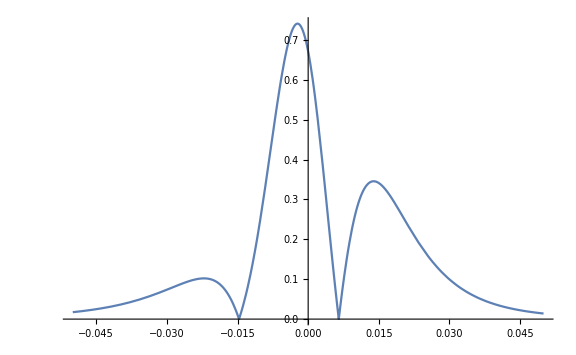

```mathematica
Plot[((Force[x, 0,-0.02,  0, -(90-24.5)/180 Pi+Pi, 0, 0, 2.07, 0.19 ][[1]])^2+(Force[x, 0,-0.02,  0, -(90-24.5)/180 Pi+Pi, 0, 0, 2.07, 0.19 ][[2]])^2)^(1/2), {x, -0.05, 0.05}, PlotLegends->BarLegend[{Automatic,{-10, 0.6}}] , PlotRange->All]
```

```mathematica
Force[x, 0,-0.02,  0, -(90-24.5)/180 Pi+Pi, 0, 0,  p1, p2 ][[1]] /. Abs->RemoveAbs//FullSimplify
```

(p1 p2 (-2.18391×10^-12+x (1.99053×10^-10+(2.18391×10^-8-1.24408×10^-7 x) x)))/((0.0004+x^2)^(7/2))

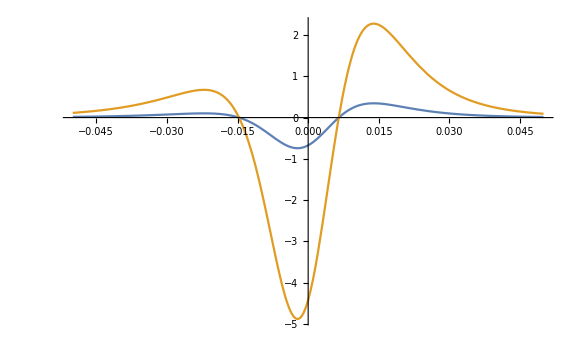

```mathematica
Plot[{(Force[x, 0,-0.02,  0, -(90-24.5)/180 Pi+Pi, 0, 0,  2.07, 0.19 ][[1]]), (Force[x, 0,-0.02,  0, -(90-24.5)/180 Pi+Pi, 0, 0,  2.07, 1.25 ][[1]])}, {x, -0.05, 0.05}, PlotLegends->BarLegend[{Automatic,{-10, 0.6}}] , PlotRange->All]
```

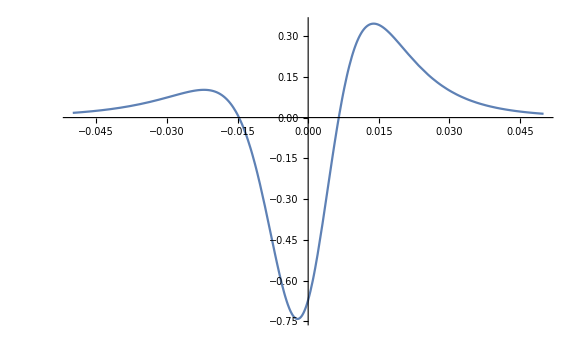

```mathematica
Plot[{(Force[x , 0,-0.02,  0, -(90-24.5)/180 Pi+Pi, 0, 0,  2.07, 0.19 ][[1]])}, {x, -0.05, 0.05}, PlotLegends->BarLegend[{Automatic,{-10, 0.6}}] , PlotRange->All]
```

```mathematica
LinearModelFit[{{0.0115, 0.1534}, {0.0059, 0.598}}, x, x]
```

FittedModel[1.06642-79.3929 x]

```mathematica
LinearModelFit[{{0.015, 0.01}, {0.005, 4.4}}, x, x]
```

FittedModel[6.595-439. x]

```mathematica
Clear[r]
```

```mathematica
Manipulate[Plot[{(2 Pi)/(√((1.0664-79.39 r)/(m r))), (2 Pi)/(√((6.595-439 r)/(m r)))}, {m,0, 0.03}], {r, 0.0001, 0.01}]
```

```mathematica
ForceCorr[F_]:=Module[{},
If[F[[3]]<=10^-3, Return[{0, 0 ,0}],Return[F]]
]
```

```mathematica
Manipulate[Graphics3D[{{Red, Arrow[{{0,  0, 0},m1[t,0, 2]}]}},Axes->True, PlotRange->{{-1.7, 1.7}, {-1.7, 1.7}, {-1.7, 1.7}} ], {t,0, 2Pi}]
```

```mathematica
(*Manipulate[
Grid[
{
{
Show[
VectorPlot[Force[x, 0,z,0, -(90-24.5)/180Pi+Pi, 0, ϕ2, 2.07, 0.19][[1;;3;;2]] ,{x, z}∈ℛ, ImageSize->Medium, VectorScaling->"Automatic", FrameLabel->{"x", "z"},PlotLegends->BarLegend[{Automatic,{0.01,0.20}}], PlotRange->{{-0.05, 0.05}, {-0.05, 0.05}}], Graphics[{{Arrowheads[Large], Darker[Red], Arrow[{8 10^-3{-Sin[ -(90-24.5)/180Pi+Pi], -Cos[ -(90-24.5)/180Pi+Pi]}, 8 10^-3{Sin[ -(90-24.5)/180Pi+Pi], Cos[ -(90-24.5)/180Pi+Pi]}}]}}]
],
 Graphics[{{GrayLevel[.89],Disk[{0, 0}, 1]}, {Arrowheads[Large], Darker[Red], Arrow[{{-Sin[ϕ2], -Cos[ϕ2]}, {Sin[ϕ2], Cos[ϕ2]}}]}}]
}
}
], 
{ϕ2, 0, 2Pi}
]*)
```

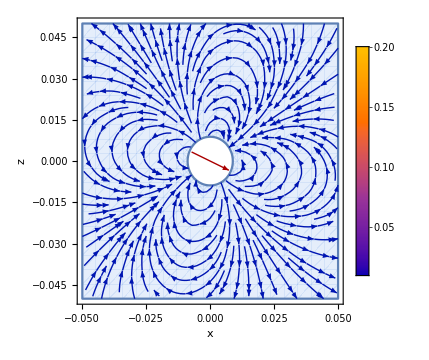

```mathematica
Show[
StreamPlot[Force[x, 0,z,0, -(90-24.5)/180 Pi+Pi, 0, 0, 2.07, 0.19][[1;;3;;2]] ,{x, z}∈ℛ, ImageSize->Medium, VectorScaling->"Automatic", FrameLabel->{"x", "z"},PlotLegends->BarLegend[{Automatic,{0.01,0.20}}], PlotRange->{{-0.05, 0.05}, {-0.05, 0.05}}], Graphics[{{Arrowheads[Large], Darker[Red], Arrow[{8 10^-3{-Sin[ -(90-24.5)/180 Pi+Pi], -Cos[ -(90-24.5)/180 Pi+Pi]}, 8 10^-3{Sin[ -(90-24.5)/180 Pi+Pi], Cos[ -(90-24.5)/180 Pi+Pi]}}]}}]
]
```

```mathematica
intF[x_,y_, z_, θ_]=Integrate[Force[x, y,z,ϕ, θ, 0, 0, 2.07, 0.19][[3]]/. Abs->RemoveAbs//FullSimplify, {ϕ, 0, 2Pi}]
```

(z Cos[θ] (-3.70677×10^-6 z^2+2.22406×10^-6 RemoveAbs[x]^2+2.22406×10^-6 RemoveAbs[y]^2+2.22406×10^-6 RemoveAbs[z]^2))/((RemoveAbs[x]^2+RemoveAbs[y]^2+RemoveAbs[z]^2)^(7/2))

```mathematica
Manipulate[Plot3D[{intF[x,y, z, θ]/(2Pi), M g}, {x, -0.05, 0.05},  {z, -0.05, 0.05}, AxesLabel->{"X", "Z", "F"}], {y, -0.05, 0.05}, {θ, 0, 2Pi}]
```

```mathematica
Manipulate[Plot3D[{int1[x,y, z, θ]/(2Pi), M g}, {x, -0.05, 0.05},  {y, -0.05, 0.05}, AxesLabel->{"X", "Y", "F"}], {z, -0.05, 0.05}, {θ, 0, 2Pi}]
```

```mathematica
Show[
StreamPlot[Force[x, 0,z,0, -(90-24.5)/180 Pi+Pi, 0, 0, 2.07, 0.19][[1;;3;;2]] ,{x, z}∈ℛ, ImageSize->Medium, VectorScaling->"Automatic", FrameLabel->{"x", "z"},PlotLegends->BarLegend[{Automatic,{0.01,0.20}}], PlotRange->{{-0.05, 0.05}, {-0.05, 0.05}}], Graphics[{{Arrowheads[Large], Darker[Red], Arrow[{8 10^-3{-Sin[ -(90-24.5)/180 Pi+Pi], -Cos[ -(90-24.5)/180 Pi+Pi]}, 8 10^-3{Sin[ -(90-24.5)/180 Pi+Pi], Cos[ -(90-24.5)/180 Pi+Pi]}}]}}]
]
```

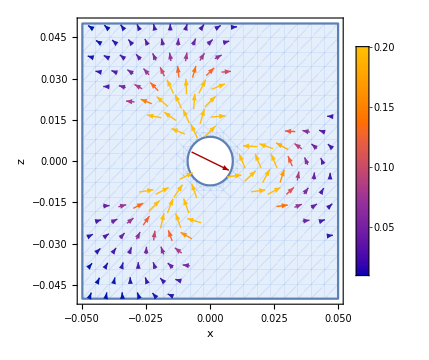

```mathematica
Show[
VectorPlot[ForceCorr[Force[x, 0,z,0, -(90-24.5)/180 Pi+Pi, 0, 0, 2.07, 0.19]][[1;;3;;2]],{x, z}∈ℛ, ImageSize->Medium, VectorScaling->"Automatic", FrameLabel->{"x", "z"},PlotLegends->BarLegend[{Automatic,{0.01,0.20}}], PlotRange->{{-0.05, 0.05}, {-0.05, 0.05}}], Graphics[{{Arrowheads[Large], Darker[Red], Arrow[{8 10^-3{-Sin[ -(90-24.5)/180 Pi+Pi], -Cos[ -(90-24.5)/180 Pi+Pi]}, 8 10^-3{Sin[ -(90-24.5)/180 Pi+Pi], Cos[ -(90-24.5)/180 Pi+Pi]}}]}}]
]
```

```mathematica
Thickness
```

```mathematica
Degree[-(90-24.5)/180 Pi+Pi]
```

°[1.9984]

```mathematica
Manipulate[
Show[
VectorPlot[ForceCorr[Force[x, 0,z,ϕ, Pi/6, 0, 0, 2.07, 0.19]][[1;;3;;2]],{x, z}∈ℛ, ImageSize->Medium, VectorScaling->"Automatic", FrameLabel->{"x", "z"},PlotLegends->BarLegend[{Automatic,{0.01,0.20}}], PlotRange->{{-0.05, 0.05}, {-0.05, 0.05}}], Graphics[{{Arrowheads[Large], Darker[Red], Arrow[{8 10^-3{-Sin[0], -Cos[ 0]}, 8 10^-3{Sin[0], Cos[ 0]}}]}}]
]
,{ϕ, 0, 2Pi}
];
```

```mathematica
Manipulate[
Show[
VectorPlot[ForceCorr[Force[x, 0,z,ϕ, Pi/6, 0, 0, 2.07, 0.19]][[1;;3;;2]],{x, z}∈ℛ, ImageSize->Medium, VectorScaling->"Automatic", FrameLabel->{"x", "z"},PlotLegends->BarLegend[{Automatic,{0.01,0.20}}], PlotRange->{{-0.05, 0.05}, {-0.05, 0.05}}]
]
,{ϕ, 0, 2Pi}
]
```

VectorPlot::idomdim: {x,z}∈ℛ does not have a valid dimension as a plotting domain.

Show::gtype: VectorPlot is not a type of graphics.

VectorPlot::idomdim: {x,z}∈ℛ does not have a valid dimension as a plotting domain.

Show::gtype: VectorPlot is not a type of graphics.

VectorPlot::idomdim: {x,z}∈ℛ does not have a valid dimension as a plotting domain.

Show::gtype: VectorPlot is not a type of graphics.

```mathematica
Export["/Users/kuleshovladimir/Desktop/Problems/2023/IPT/16. Unstable levitation/Videos/horisontal rotation.mp4", %152];
```

```mathematica
(*Manipulate[
Grid[
{
{
Show[
VectorPlot[ForceCorr[Force[x, 0,z,0, -(90-24.5)/180Pi+Pi, 0, ϕ2, 2.07, 0.19]][[1;;3;;2]],{x, z}∈ℛ, ImageSize->Medium, VectorScaling->"Automatic", FrameLabel->{"x", "z"},PlotLegends->BarLegend[{Automatic,{0.01,0.20}}], PlotRange->{{-0.05, 0.05}, {-0.05, 0.05}}], Graphics[{{Arrowheads[Large], Darker[Red], Arrow[{8 10^-3{-Sin[ -(90-24.5)/180Pi+Pi], -Cos[ -(90-24.5)/180Pi+Pi]}, 8 10^-3{Sin[ -(90-24.5)/180Pi+Pi], Cos[ -(90-24.5)/180Pi+Pi]}}]}}]
],
 Graphics[{{GrayLevel[.89],Disk[{0, 0}, 1]}, {Arrowheads[Large], Darker[Red], Arrow[{{-Sin[ϕ2], -Cos[ϕ2]}, {Sin[ϕ2], Cos[ϕ2]}}]}}]
}
}
], 
{ϕ2, 0, 2Pi}
]*)
```

```mathematica
(*Manipulate[Grid[{{
VectorPlot[ForceCorr[Force[x, 0,z,θ1, -(90-24.5)/180Pi+Pi, 0, ϕ2, 2.07, 0.19]][[1;;3;;2]],{x,- 0.05,0.05},{z,-0.05,0.05}, ImageSize->Medium, VectorScaling->"Linear", FrameLabel->{"x", "z"},PlotLegends->BarLegend[{Automatic,{0.5,4}}]], Graphics[{{GrayLevel[.89],Disk[{0, 0}, 1]}, {Arrowheads[Large], Darker[Red], Arrow[{{-Sin[ϕ2], -Cos[ϕ2]}, {Sin[ϕ2], Cos[ϕ2]}}]}}]
}}
]
, {ϕ2, 0, 2Pi}, {θ1, 0, 2Pi}
]*)
```

### Energy

```mathematica
Ufield[x_, y_,z_, θ1_, ϕ1_, θ2_, ϕ2_,  p1_, p2_]:=μ0/(4Pi)((m1[θ1, ϕ1, p1].m2[θ2, ϕ2, p2])/Norm[r2[x, y, z]]^3-(3 (m1[θ1, ϕ1, p1].r2[x, y, z])(m2[θ2, ϕ2, p2].r2[x, y, z]))/Norm[r2[x, y, z]]^5)
```

```mathematica
intU[x_,y_, z_, θ_, c_]=Integrate[Ufield[x, y,z,ϕ, θ, ϕ+c, 75/180 Pi,  2.07, 0.19]/. Abs->RemoveAbs//FullSimplify, {ϕ, 0, 2Pi}]
```

1/((x^2+y^2+z^2)^(5/2))((6.39588×10^-8 x^2+6.39588×10^-8 y^2-1.27918×10^-7 z^2) Cos[θ]+(1.79023×10^-7 x^2+1.79023×10^-7 y^2) Sin[c-1. θ]+2.38697×10^-7 x^2 Cos[c] Sin[θ]+2.38697×10^-7 y^2 Cos[c] Sin[θ]+2.38697×10^-7 z^2 Cos[c] Sin[θ]+2.79145×10^-23 x y Sin[c] Sin[θ]-1.79023×10^-7 x^2 Sin[c+θ]-1.79023×10^-7 y^2 Sin[c+θ])

```mathematica
Manipulate[Plot3D[intU[x,y, z, θ, c]/(2Pi)+M g z, {x, -0.05, 0.05},  {z, -0.05, 0.05}, AxesLabel->{"X", "Z", "U"}], {y, -0.05, 0.05}, {θ, 0, 2Pi}, {c, 0, 2Pi}]
```

```mathematica
Manipulate[Plot3D[intU[x,y, z, θ, c]/(2Pi)+M g z, {x, -0.05, 0.05},  {z, -0.05, 0.05}, ColorFunction->"GrayYellowTones",PlotLegends->BarLegend[{Automatic,{-0.015, 0}}, 60], PlotRange->{{-0.05, 0.05},{-0.05, 0}, {-0.015, 0}}, AxesLabel->{"X", "Z", "U"}], {{y, -0.01}, -0.05, 0.05}, {{θ, 5.74}, 0, 2Pi}, {c, 0, 2Pi}]
```

```mathematica
Manipulate[
ContourPlot[
intU[x,y, z, θ, c]/(2Pi)+M g z, 
{x, -0.05, 0.05},  {z, -0.05, 0}, ColorFunction->"GrayYellowTones",PlotLegends->BarLegend[{Automatic,{-0.015, 0}}, 60], PlotRange-> {-0.015, 0}, ClippingStyle->Automatic
], {{y, -0.007}, -0.05, 0.05}, {{θ, 5.74}, 0, 2Pi}, {c, 0, 2Pi}
]
```

```mathematica
Manipulate[Show[ContourPlot[Ufield[x, z,-0.02,  t, -(90-24.5)/180 Pi+Pi, 0, 0, 2.07, 0.19 ]- M g z, {x, z}∈ℛ, PlotLegends->BarLegend[{Automatic,{-0.005, 0.0021}}], Contours->10], VectorPlot[Force[x, z,-0.02,t, -(90-24.5)/180 Pi+Pi, 0, 0, 2.07, 0.19][[1;;2]] ,{x, z}∈ℛ, ImageSize->Medium, VectorScaling->"Automatic", FrameLabel->{"x", "z"},PlotLegends->BarLegend[{Automatic,{0.01,0.20}}], PlotRange->{{-0.05, 0.05}, {-0.05, 0.05}}]], {t, 0, 2Pi, 0.1}]
```

ContourPlot::idomdim: {x,z}∈ℛ does not have a valid dimension as a plotting domain.

VectorPlot::idomdim: {x,z}∈ℛ does not have a valid dimension as a plotting domain.

Show::gcomb: Could not combine the graphics objects in ….

```mathematica
Plot[]
```

```mathematica
Manipulate[Show[ContourPlot[Ufield[x, y,-0.02,  t, -(90-24.5)/180 Pi+Pi, 0, 0, 2.07, 0.19 ]+M g 0.02, {x, y}∈ℛ, PlotLegends->BarLegend[{Automatic,{-0.0005, 0.0021}}], Contours->10]], {t, 0, 2Pi, 0.1}]
```

ContourPlot::idomdim: {x,y}∈ℛ does not have a valid dimension as a plotting domain.

Show::gtype: ContourPlot is not a type of graphics.

ContourPlot::idomdim: {x,y}∈ℛ does not have a valid dimension as a plotting domain.

Show::gtype: ContourPlot is not a type of graphics.

```mathematica
Export["/Users/kuleshovladimir/Desktop/Problems/2023/IPT/16. Unstable levitation/energy.mp4", %212]
```

/Users/kuleshovladimir/Desktop/Problems/2023/IPT/16. Unstable levitation/energy.mp4

```mathematica
simulation[M_, tFinish_, x0_, y0_, z0_,δz_, vxStart_,vyStart_, ω0_]:=Module[{nds},
nds=NDSolve[
{
Force[x[t],y[t],z[t],ω0 t, -(90-24.5)/180 Pi+Pi, 0, 0, 2.07, 0.19][[1]] == M x''[t], x[0]==x0, x'[0]==vxStart,
Force[x[t],y[t],z[t],ω0 t, -(90-24.5)/180 Pi+Pi, 0, 0, 2.07, 0.19][[2]] == M y''[t], y[0]== y0, y'[0]==vyStart,
Force[x[t],y[t],z[t],ω0 t, -(90-24.5)/180 Pi+Pi, 0, 0, 2.07, 0.19][[3]] - M g == M z''[t], z[0]==z0, z'[0]==0
}
,{x, y, z}
, {t, 0,tFinish}
];
Return@nds
(*Show[
(*ContourPlot[Ufield[x, z,-0.02,  0, -(90-24.5)/180Pi+Pi, 0, 0, 2.07, 0.19 ]- M g z, {x, z}∈ℛ, PlotLegends->BarLegend[{Automatic,{-0.005, 0.0021}}], Contours->10],*)
ParametricPlot3D[Evaluate[{x[t], y[t], z[t]}/.nds],{t, 0.0001, tFinish},  PlotStyle->Darker[Green], Axes->False],
PlotRange->{{-0.05, 0.05}, {-0.05, 0.05}}, AxesOrigin->{0, 0}
]*)
]
```

```mathematica
Manipulate[ParametricPlot[Evaluate[{x[t], y[t]}/.simulation[m, tFin,x0 ,y0, -0.005,0, vxStart, vyStart, ω0]],{t, 0, tFin},  PlotStyle->Darker[Green], Axes->True, PlotRange->{{-0.05, 0.05},{-0.05, 0.05}}],
{{m, 0.00286}, 0.001, 0.0035},{{ω0, 526}, 100, 800},{{x0, -0.0153}, -0.02, 0.02}, {{y0, -0.0128}, -0.02, 0.02},  {{z0, -0.00135}, -0.002, -0.001}, {{vxStart, -0.96}, -5, 5}, {{vyStart, 0.76}, -5, 5}, {{tFin, 0.18}, 0.001, 0.62}
]
```

ReplaceAll::reps: {simulation[0.00286,0.21,-0.0153,-0.0128,-0.005,0,-0.96,0.76,526]} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

ReplaceAll::reps: {simulation[0.00286,0.21,-0.0153,-0.0128,-0.005,0.,-0.96,0.76,526.]} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

General::stop: Further output of ReplaceAll::reps will be suppressed during this calculation.

ReplaceAll::reps: {simulation[0.00286,0.21,-0.0153,-0.0128,-0.005,0,-0.96,0.76,526]} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

ReplaceAll::reps: {simulation[0.00286,0.21,-0.0153,-0.0128,-0.005,0.,-0.96,0.76,526.]} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

General::stop: Further output of ReplaceAll::reps will be suppressed during this calculation.

ReplaceAll::reps: {simulation[0.00286,0.21,-0.0153,-0.0128,-0.005,0,-0.96,0.76,526]} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

ReplaceAll::reps: {simulation[0.00286,0.21,-0.0153,-0.0128,-0.005,0.,-0.96,0.76,526.]} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

General::stop: Further output of ReplaceAll::reps will be suppressed during this calculation.

ReplaceAll::reps: {simulation[0.00286,0.21,-0.0153,-0.0128,-0.005,0,-0.96,0.76,526]} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

ReplaceAll::reps: {simulation[0.00286,0.21,-0.0153,-0.0128,-0.005,0.,-0.96,0.76,526.]} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

General::stop: Further output of ReplaceAll::reps will be suppressed during this calculation.

ReplaceAll::reps: {simulation[0.00286,0.21,-0.0153,-0.0128,-0.005,0,-0.96,0.76,526]} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

ReplaceAll::reps: {simulation[0.00286,0.21,-0.0153,-0.0128,-0.005,0.,-0.96,0.76,526.]} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

General::stop: Further output of ReplaceAll::reps will be suppressed during this calculation.

ReplaceAll::reps: {simulation[0.00286,0.21,-0.0153,-0.0128,-0.005,0,-0.96,0.76,526]} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

ReplaceAll::reps: {simulation[0.00286,0.21,-0.0153,-0.0128,-0.005,0.,-0.96,0.76,526.]} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

General::stop: Further output of ReplaceAll::reps will be suppressed during this calculation.

ReplaceAll::reps: {simulation[0.00286,0.21,-0.0153,-0.0128,-0.005,0,-0.96,0.76,526]} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

ReplaceAll::reps: {simulation[0.00286,0.21,-0.0153,-0.0128,-0.005,0.,-0.96,0.76,526.]} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

General::stop: Further output of ReplaceAll::reps will be suppressed during this calculation.

```mathematica
simulation1[M_, tFinish_, x0_, y0_, z0_,δz_, vxStart_,vyStart_, ω0_]:=Module[{nds},
nds=NDSolve[
{
Force[x[t], y[t],-0.005,ω0 t,  -(90-24.5)/180 Pi+Pi, 0, 0, 2.07 , 0.19][[1]] == M x''[t], x[0]==x0, x'[0]==vxStart,
Force[x[t], y[t],-0.005,ω0 t ,  -(90-24.5)/180 Pi+Pi, 0, 0, 2.07 , 0.19][[2]] == M y''[t], y[0]== y0, y'[0]==vyStart
}
,{x, y}
, {t, 0,tFinish}
];
Return@nds
]
```

```mathematica
Manipulate[
Show[
ParametricPlot[
Evaluate[{x[t], y[t]}/.simulation1[m, tFin,r Cos[Ψ] ,r Sin[Ψ], -0.005,0,- a ω0 r Cos[Pi/2-Ψ], a ω0 r Sin[Pi/2-Ψ], ω0]],{t, 0, tFin},  PlotStyle->Darker[Green], PlotRange->{{-0.01, 0.01},{-0.01, 0.01}}
](*,
Graphics[
Arrow[{Evaluate[{x[tFin], y[tFin]}/.simulation1[m, tFin,r Cos[Ψ] ,r Sin[Ψ], -0.005,0,  ω0 r Cos[Pi/2-Ψ],  ω0 r Sin[Pi/2-Ψ], ω0]][[1]], Evaluate[{Force[x[tFin],y[tFin], -0.005,ω0 tFin,-(90-24.5)/180Pi+Pi,  0, 0, 2.07 , 0.19][[1]] 0.0001, Force[x[tFin],y[tFin], -0.005,ω0 tFin,-(90-24.5)/180Pi+Pi,  0, 0, 2.07 , 0.19][[2]] 0.0001}/.simulation1[m, tFin,r Cos[Ψ] ,r Sin[Ψ], -0.005,0,  ω0 r Cos[Pi/2-Ψ],  ω0 r Sin[Pi/2-Ψ], ω0]][[1]]}]
]*)
, Frame->True],
{{m, 0.0032}, 0.001, 0.035},{{ω0, 526}, 0, 1000}, {{r, 0.00281}, 0, 0.03}, {{Ψ,Pi},0, 2Pi},{{a, 2.22}, 2, 3}, {{tFin, 0.1}, 0.001, 0.1}
]
```

Dot::rect: Nonrectangular tensor encountered.

General::stop: Further output of Dot::rect will be suppressed during this calculation.

NDSolve::dsvar: {0,2} cannot be used as a variable.

ReplaceAll::reps: {NDSolve[«1»]} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

NDSolve::dsvar: {0,2} cannot be used as a variable.

ReplaceAll::reps: {NDSolve[«1»]} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

NDSolve::dsvar: {0.,2.} cannot be used as a variable.

General::stop: Further output of NDSolve::dsvar will be suppressed during this calculation.

ReplaceAll::reps: … is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

General::stop: Further output of ReplaceAll::reps will be suppressed during this calculation.

Dot::rect: Nonrectangular tensor encountered.

General::stop: Further output of Dot::rect will be suppressed during this calculation.

NDSolve::dsvar: {0,2} cannot be used as a variable.

ReplaceAll::reps: {NDSolve[«1»]} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

NDSolve::dsvar: {0,2} cannot be used as a variable.

ReplaceAll::reps: {NDSolve[«1»]} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

NDSolve::dsvar: {0.,2.} cannot be used as a variable.

General::stop: Further output of NDSolve::dsvar will be suppressed during this calculation.

ReplaceAll::reps: … is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

General::stop: Further output of ReplaceAll::reps will be suppressed during this calculation.

Dot::rect: Nonrectangular tensor encountered.

General::stop: Further output of Dot::rect will be suppressed during this calculation.

NDSolve::dsvar: {0,2} cannot be used as a variable.

ReplaceAll::reps: {NDSolve[«1»]} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

NDSolve::dsvar: {0,2} cannot be used as a variable.

ReplaceAll::reps: {NDSolve[«1»]} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

NDSolve::dsvar: {0.,2.} cannot be used as a variable.

General::stop: Further output of NDSolve::dsvar will be suppressed during this calculation.

ReplaceAll::reps: … is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

General::stop: Further output of ReplaceAll::reps will be suppressed during this calculation.

Dot::rect: Nonrectangular tensor encountered.

General::stop: Further output of Dot::rect will be suppressed during this calculation.

NDSolve::dsvar: {0,2} cannot be used as a variable.

ReplaceAll::reps: {NDSolve[«1»]} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

NDSolve::dsvar: {0,2} cannot be used as a variable.

ReplaceAll::reps: {NDSolve[«1»]} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

NDSolve::dsvar: {0.,2.} cannot be used as a variable.

General::stop: Further output of NDSolve::dsvar will be suppressed during this calculation.

ReplaceAll::reps: … is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

General::stop: Further output of ReplaceAll::reps will be suppressed during this calculation.

Dot::rect: Nonrectangular tensor encountered.

General::stop: Further output of Dot::rect will be suppressed during this calculation.

NDSolve::dsvar: {0,2} cannot be used as a variable.

ReplaceAll::reps: {NDSolve[«1»]} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

NDSolve::dsvar: {0,2} cannot be used as a variable.

ReplaceAll::reps: {NDSolve[«1»]} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

NDSolve::dsvar: {0.,2.} cannot be used as a variable.

General::stop: Further output of NDSolve::dsvar will be suppressed during this calculation.

ReplaceAll::reps: … is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

General::stop: Further output of ReplaceAll::reps will be suppressed during this calculation.

ReplaceAll::reps: {simulation1[0.02225,0.0423,-0.00506704,0.00330569,-0.005,0,-2.2603,-3.46464,308.]} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

ReplaceAll::reps: {simulation1[0.02225,0.0423,-0.00506704,0.00330569,-0.005,0.,-2.2603,-3.46464,308.]} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

General::stop: Further output of ReplaceAll::reps will be suppressed during this calculation.

```mathematica
Manipulate[
Show[
ParametricPlot3D[
Evaluate[{x[t], y[t],-0.005+ 0.001 Cos[10000 t]}/.simulation1[m, tFin,r Cos[Ψ] ,r Sin[Ψ], -0.005,0,- a ω0 r Cos[Pi/2-Ψ], a ω0 r Sin[Pi/2-Ψ], ω0]],{t, 0, tFin},  PlotStyle->Darker[Green], PlotRange->{{-0.01, 0.01},{-0.01, 0.01},{-0.008, 0}}
](*,
Graphics[
Arrow[{Evaluate[{x[tFin], y[tFin]}/.simulation1[m, tFin,r Cos[Ψ] ,r Sin[Ψ], -0.005,0,  ω0 r Cos[Pi/2-Ψ],  ω0 r Sin[Pi/2-Ψ], ω0]][[1]], Evaluate[{Force[x[tFin],y[tFin], -0.005,ω0 tFin,-(90-24.5)/180Pi+Pi,  0, 0, 2.07 , 0.19][[1]] 0.0001, Force[x[tFin],y[tFin], -0.005,ω0 tFin,-(90-24.5)/180Pi+Pi,  0, 0, 2.07 , 0.19][[2]] 0.0001}/.simulation1[m, tFin,r Cos[Ψ] ,r Sin[Ψ], -0.005,0,  ω0 r Cos[Pi/2-Ψ],  ω0 r Sin[Pi/2-Ψ], ω0]][[1]]}]
]*)
, Frame->True],
{{m, 0.0032}, 0.001, 0.035},{{ω0, 526}, 0, 1000}, {{r, 0.00281}, 0, 0.03}, {{Ψ,Pi},0, 2Pi},{{a, 2.22}, 2, 3}, {{tFin, 0.1}, 0.001, 0.1}
]
```

Dot::rect: Nonrectangular tensor encountered.

General::stop: Further output of Dot::rect will be suppressed during this calculation.

NDSolve::dsvar: {0,2} cannot be used as a variable.

ReplaceAll::reps: … is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

NDSolve::dsvar: {0,2} cannot be used as a variable.

ReplaceAll::reps: … is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

NDSolve::dsvar: {0.,2.} cannot be used as a variable.

General::stop: Further output of NDSolve::dsvar will be suppressed during this calculation.

ReplaceAll::reps: {NDSolve[«1»]} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

General::stop: Further output of ReplaceAll::reps will be suppressed during this calculation.

Dot::rect: Nonrectangular tensor encountered.

General::stop: Further output of Dot::rect will be suppressed during this calculation.

NDSolve::dsvar: {0,2} cannot be used as a variable.

ReplaceAll::reps: … is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

NDSolve::dsvar: {0,2} cannot be used as a variable.

ReplaceAll::reps: … is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

NDSolve::dsvar: {0.,2.} cannot be used as a variable.

General::stop: Further output of NDSolve::dsvar will be suppressed during this calculation.

ReplaceAll::reps: {NDSolve[«1»]} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

General::stop: Further output of ReplaceAll::reps will be suppressed during this calculation.

Dot::rect: Nonrectangular tensor encountered.

General::stop: Further output of Dot::rect will be suppressed during this calculation.

NDSolve::dsvar: {0,2} cannot be used as a variable.

ReplaceAll::reps: … is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

NDSolve::dsvar: {0,2} cannot be used as a variable.

ReplaceAll::reps: … is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

NDSolve::dsvar: {0.,2.} cannot be used as a variable.

General::stop: Further output of NDSolve::dsvar will be suppressed during this calculation.

ReplaceAll::reps: {NDSolve[«1»]} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

General::stop: Further output of ReplaceAll::reps will be suppressed during this calculation.

Dot::rect: Nonrectangular tensor encountered.

General::stop: Further output of Dot::rect will be suppressed during this calculation.

NDSolve::dsvar: {0,2} cannot be used as a variable.

ReplaceAll::reps: … is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

NDSolve::dsvar: {0,2} cannot be used as a variable.

ReplaceAll::reps: … is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

NDSolve::dsvar: {0.,2.} cannot be used as a variable.

General::stop: Further output of NDSolve::dsvar will be suppressed during this calculation.

ReplaceAll::reps: {NDSolve[«1»]} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

General::stop: Further output of ReplaceAll::reps will be suppressed during this calculation.

Dot::rect: Nonrectangular tensor encountered.

General::stop: Further output of Dot::rect will be suppressed during this calculation.

NDSolve::dsvar: {0,2} cannot be used as a variable.

ReplaceAll::reps: … is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

NDSolve::dsvar: {0,2} cannot be used as a variable.

ReplaceAll::reps: … is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

NDSolve::dsvar: {0.,2.} cannot be used as a variable.

General::stop: Further output of NDSolve::dsvar will be suppressed during this calculation.

ReplaceAll::reps: {NDSolve[«1»]} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

General::stop: Further output of ReplaceAll::reps will be suppressed during this calculation.

ReplaceAll::reps: {simulation1[0.0032,0.1,-0.00455,0.,-0.005,0,0.,-5.31313,526]} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

ReplaceAll::reps: {simulation1[0.0032,0.1,-0.00455,0.,-0.005,0.,0.,-5.31313,526.]} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

General::stop: Further output of ReplaceAll::reps will be suppressed during this calculation.

```mathematica
simulation2[M_, tFinish_, x0_, y0_, z0_,δz_, vxStart_,vyStart_,vzStart_, ω0_]:=Module[{nds},
nds=NDSolve[
{
Force[x[t], y[t],z[t],ω0 t,  -(90-24.5)/180 Pi+Pi, 0, 0, 2.07 , 0.19][[1]] == M x''[t], x[0]==x0, x'[0]==vxStart,
Force[x[t], y[t],z[t],ω0 t ,  -(90-24.5)/180 Pi+Pi, 0, 0, 2.07 , 0.19][[2]] == M y''[t], y[0]== y0, y'[0]==vyStart,
Force[x[t], y[t],z[t],ω0 t ,  -(90-24.5)/180 Pi+Pi, 0, 0, 2.07 , 0.19][[3]]-M g == M z''[t], z[0]== z0, z'[0]==vzStart
}
,{x, y, z}
, {t, 0,tFinish}
];
Return@nds
]
```

```mathematica
Manipulate[
Show[
ParametricPlot[
Evaluate[{x[t], y[t]}/.simulation2[m, tFin,r Cos[Ψ] ,r Sin[Ψ], -0.005,0,- a ω0 r Cos[Pi/2-Ψ], a ω0 r Sin[Pi/2-Ψ],vzStart,  ω0]],{t, 0, tFin},  PlotStyle->Darker[Green], PlotRange->{{-0.01, 0.01},{-0.01, 0.01}}
]
, Frame->True],
{{m, 0.0032}, 0.001, 0.035},{{ω0, 526}, 0, 1000}, {{r, 0.00281}, 0, 0.03}, {{Ψ,Pi},0, 2Pi},{{a, 2.22}, 2, 3}, {{vzStart, 0},-5, 5 }, {{tFin, 0.1}, 0.001, 0.1}
]
```

NDSolve::ndsz: At t == 0.000451294, step size is effectively zero; singularity or stiff system suspected.

NDSolve::ndsz: At t == 0.000722755, step size is effectively zero; singularity or stiff system suspected.

NDSolve::ndsz: At t == 0.000689309, step size is effectively zero; singularity or stiff system suspected.

NDSolve::ndsz: At t == 0.000858675, step size is effectively zero; singularity or stiff system suspected.

NDSolve::ndsz: At t == 0.000862204, step size is effectively zero; singularity or stiff system suspected.

NDSolve::ndsz: At t == 0.000688348, step size is effectively zero; singularity or stiff system suspected.

NDSolve::ndsz: At t == 0.000721286, step size is effectively zero; singularity or stiff system suspected.

NDSolve::ndsz: At t == 0.000750992, step size is effectively zero; singularity or stiff system suspected.

NDSolve::ndsz: At t == 0.000782183, step size is effectively zero; singularity or stiff system suspected.

NDSolve::ndsz: At t == 0.00216612, step size is effectively zero; singularity or stiff system suspected.

NDSolve::ndsz: At t == 0.00260921, step size is effectively zero; singularity or stiff system suspected.

NDSolve::ndsz: At t == 0.00295577, step size is effectively zero; singularity or stiff system suspected.

NDSolve::ndsz: At t == 0.00209426, step size is effectively zero; singularity or stiff system suspected.

NDSolve::ndsz: At t == 0.00147191, step size is effectively zero; singularity or stiff system suspected.

NDSolve::ndsz: At t == 0.00146697, step size is effectively zero; singularity or stiff system suspected.

ReplaceAll::reps: {simulation2[0.0075,0.0046,-0.00444859,0.000111829,-0.005,0,-0.200027,-7.95716,5.,654.]} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

ReplaceAll::reps: {simulation2[0.0075,0.0046,-0.00444859,0.000111829,-0.005,0.,-0.200027,-7.95716,5.,654.]} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

General::stop: Further output of ReplaceAll::reps will be suppressed during this calculation.

ReplaceAll::reps: {simulation2[0.0075,0.0046,-0.00444859,0.000111829,-0.005,0,-0.200027,-7.95716,5.,654.]} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

ReplaceAll::reps: {simulation2[0.0075,0.0046,-0.00444859,0.000111829,-0.005,0.,-0.200027,-7.95716,5.,654.]} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

General::stop: Further output of ReplaceAll::reps will be suppressed during this calculation.

ReplaceAll::reps: {simulation2[0.0075,0.0046,-0.00444859,0.000111829,-0.005,0,-0.200027,-7.95716,5.,654.]} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

ReplaceAll::reps: {simulation2[0.0075,0.0046,-0.00444859,0.000111829,-0.005,0.,-0.200027,-7.95716,5.,654.]} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

General::stop: Further output of ReplaceAll::reps will be suppressed during this calculation.

ReplaceAll::reps: {simulation2[0.0075,0.0046,-0.00444859,0.000111829,-0.005,0,-0.200027,-7.95716,5.,654.]} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

ReplaceAll::reps: {simulation2[0.0075,0.0046,-0.00444859,0.000111829,-0.005,0.,-0.200027,-7.95716,5.,654.]} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

General::stop: Further output of ReplaceAll::reps will be suppressed during this calculation.

ReplaceAll::reps: {simulation2[0.0075,0.0046,-0.00444859,0.000111829,-0.005,0,-0.200027,-7.95716,5.,654.]} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

ReplaceAll::reps: {simulation2[0.0075,0.0046,-0.00444859,0.000111829,-0.005,0.,-0.200027,-7.95716,5.,654.]} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

General::stop: Further output of ReplaceAll::reps will be suppressed during this calculation.

ReplaceAll::reps: {simulation2[0.0075,0.0046,-0.00444859,0.000111829,-0.005,0,-0.200027,-7.95716,5.,654.]} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

ReplaceAll::reps: {simulation2[0.0075,0.0046,-0.00444859,0.000111829,-0.005,0.,-0.200027,-7.95716,5.,654.]} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

General::stop: Further output of ReplaceAll::reps will be suppressed during this calculation.

```mathematica
Manipulate[
Show[
Plot[
Evaluate[(z[t])/.simulation2[m, tFin,r Cos[Ψ] ,r Sin[Ψ], z0,0,- a ω0 r Cos[Pi/2-Ψ], a ω0 r Sin[Pi/2-Ψ],vzStart,  ω0]],{t, 0, tFin},  PlotStyle->Darker[Green], PlotRange->All
]],
{{m, 0.0509}, 0.001, 0.1},{{ω0,491.}, 0, 1000}, {{r, 0.0028}, 0, 0.03}, {{Ψ,Pi},0, 2Pi},{{a, 2.22}, 2, 3}, {{vzStart, 0},-5, 5 }, {{z0, -0.005}, -0.03,  -0.005},{{tFin, 0.1}, 0.001, 0.5}
]
```

NDSolve::ndsz: At t == 0.00430374, step size is effectively zero; singularity or stiff system suspected.

NDSolve::ndsz: At t == 0.00438434, step size is effectively zero; singularity or stiff system suspected.

NDSolve::ndsz: At t == 0.00614087, step size is effectively zero; singularity or stiff system suspected.

NDSolve::ndsz: At t == 0.00852328, step size is effectively zero; singularity or stiff system suspected.

NDSolve::ndsz: At t == 0.00787605, step size is effectively zero; singularity or stiff system suspected.

NDSolve::ndsz: At t == 0.00732192, step size is effectively zero; singularity or stiff system suspected.

NDSolve::ndsz: At t == 0.00729992, step size is effectively zero; singularity or stiff system suspected.

NDSolve::ndsz: At t == 0.00826471, step size is effectively zero; singularity or stiff system suspected.

NDSolve::ndsz: At t == 0.00136958, step size is effectively zero; singularity or stiff system suspected.

NDSolve::ndsz: At t == 0.00641895, step size is effectively zero; singularity or stiff system suspected.

NDSolve::ndsz: At t == 0.00826471, step size is effectively zero; singularity or stiff system suspected.

NDSolve::ndsz: At t == 0.00781237, step size is effectively zero; singularity or stiff system suspected.

NDSolve::ndsz: At t == 0.00800905, step size is effectively zero; singularity or stiff system suspected.

NDSolve::ndsz: At t == 0.00136937, step size is effectively zero; singularity or stiff system suspected.

NDSolve::ndsz: At t == 0.00800905, step size is effectively zero; singularity or stiff system suspected.

NDSolve::ndsz: At t == 0.0079916, step size is effectively zero; singularity or stiff system suspected.

NDSolve::ndsz: At t == 0.00802686, step size is effectively zero; singularity or stiff system suspected.

NDSolve::ndsz: At t == 0.00804505, step size is effectively zero; singularity or stiff system suspected.

NDSolve::ndsz: At t == 0.00806362, step size is effectively zero; singularity or stiff system suspected.

NDSolve::ndsz: At t == 0.00800905, step size is effectively zero; singularity or stiff system suspected.

NDSolve::ndsz: At t == 0.00832425, step size is effectively zero; singularity or stiff system suspected.

NDSolve::ndsz: At t == 0.00735636, step size is effectively zero; singularity or stiff system suspected.

ReplaceAll::reps: {simulation2[0.0509,0.5,-0.01015,0.,-0.005,0,0.,0.,0.0005,0.]} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

ReplaceAll::reps: {simulation2[0.0509,0.5,-0.01015,0.,-0.005,0.,0.,0.,0.0005,0.]} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

General::stop: Further output of ReplaceAll::reps will be suppressed during this calculation.

ReplaceAll::reps: {simulation2[0.0509,0.5,-0.01015,0.,-0.005,0,0.,0.,0.0005,0.]} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

ReplaceAll::reps: {simulation2[0.0509,0.5,-0.01015,0.,-0.005,0.,0.,0.,0.0005,0.]} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

General::stop: Further output of ReplaceAll::reps will be suppressed during this calculation.

ReplaceAll::reps: {simulation2[0.0509,0.5,-0.01015,0.,-0.005,0,0.,0.,0.0005,0.]} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

ReplaceAll::reps: {simulation2[0.0509,0.5,-0.01015,0.,-0.005,0.,0.,0.,0.0005,0.]} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

General::stop: Further output of ReplaceAll::reps will be suppressed during this calculation.

ReplaceAll::reps: {simulation2[0.0509,0.5,-0.01015,0.,-0.005,0,0.,0.,0.0005,0.]} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

ReplaceAll::reps: {simulation2[0.0509,0.5,-0.01015,0.,-0.005,0.,0.,0.,0.0005,0.]} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

General::stop: Further output of ReplaceAll::reps will be suppressed during this calculation.

ReplaceAll::reps: {simulation2[0.0509,0.5,-0.01015,0.,-0.005,0,0.,0.,0.0005,0.]} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

ReplaceAll::reps: {simulation2[0.0509,0.5,-0.01015,0.,-0.005,0.,0.,0.,0.0005,0.]} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

General::stop: Further output of ReplaceAll::reps will be suppressed during this calculation.

ReplaceAll::reps: {simulation2[0.0509,0.5,-0.01015,0.,-0.005,0,0.,0.,0.0005,0.]} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

ReplaceAll::reps: {simulation2[0.0509,0.5,-0.01015,0.,-0.005,0.,0.,0.,0.0005,0.]} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

General::stop: Further output of ReplaceAll::reps will be suppressed during this calculation.

ReplaceAll::reps: {simulation2[0.0509,0.5,-0.01015,0.,-0.005,0,0.,0.,0.0005,0.]} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

ReplaceAll::reps: {simulation2[0.0509,0.5,-0.01015,0.,-0.005,0.,0.,0.,0.0005,0.]} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

General::stop: Further output of ReplaceAll::reps will be suppressed during this calculation.

ReplaceAll::reps: {simulation2[0.0509,0.5,-0.01015,0.,-0.005,0,0.,0.,0.0005,0.]} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

ReplaceAll::reps: {simulation2[0.0509,0.5,-0.01015,0.,-0.005,0.,0.,0.,0.0005,0.]} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

General::stop: Further output of ReplaceAll::reps will be suppressed during this calculation.

ReplaceAll::reps: {simulation2[0.0509,0.5,-0.01015,0.,-0.005,0,0.,0.,0.0005,0.]} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

ReplaceAll::reps: {simulation2[0.0509,0.5,-0.01015,0.,-0.005,0.,0.,0.,0.0005,0.]} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

General::stop: Further output of ReplaceAll::reps will be suppressed during this calculation.

ReplaceAll::reps: {simulation2[0.0509,0.5,-0.01015,0.,-0.005,0,0.,0.,0.0005,0.]} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

ReplaceAll::reps: {simulation2[0.0509,0.5,-0.01015,0.,-0.005,0.,0.,0.,0.0005,0.]} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

General::stop: Further output of ReplaceAll::reps will be suppressed during this calculation.

ReplaceAll::reps: {simulation2[0.0509,0.5,-0.01015,0.,-0.005,0,0.,0.,0.0005,0.]} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

ReplaceAll::reps: {simulation2[0.0509,0.5,-0.01015,0.,-0.005,0.,0.,0.,0.0005,0.]} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

General::stop: Further output of ReplaceAll::reps will be suppressed during this calculation.

```mathematica
Manipulate[
Show[
ContourPlot[Ufield[x, y,-0.005,  ω0 tFin, -(90-24.5)/180 Pi+Pi, 0, 0, 2.07, 0.19 ]+M g 0.005, {x, -0.05, 0.05}, {y, -0.05, 0.05}, ColorFunction->"GrayYellowTones",Contours->40,PlotLegends->BarLegend[{Automatic, {-0.5,0.5}}, 40], PlotRange->{-0.5,0.5}],
ParametricPlot[
Evaluate[{x[t], y[t]}/.simulation1[m, tFin,r Cos[Ψ] ,r Sin[Ψ], -0.005,0,- a ω0 r Cos[Pi/2-Ψ], a ω0 r Sin[Pi/2-Ψ], ω0]],{t, 0, tFin},  PlotStyle->Darker[Green]
](*,
Graphics[
Arrow[{Evaluate[{x[tFin], y[tFin]}/.simulation1[m, tFin,r Cos[Ψ] ,r Sin[Ψ], -0.005,0,  ω0 r Cos[Pi/2-Ψ],  ω0 r Sin[Pi/2-Ψ], ω0]][[1]], Evaluate[{Force[x[tFin],y[tFin], -0.005,ω0 tFin,-(90-24.5)/180Pi+Pi,  0, 0, 2.07 , 0.19][[1]] 0.0001, Force[x[tFin],y[tFin], -0.005,ω0 tFin,-(90-24.5)/180Pi+Pi,  0, 0, 2.07 , 0.19][[2]] 0.0001}/.simulation1[m, tFin,r Cos[Ψ] ,r Sin[Ψ], -0.005,0,  ω0 r Cos[Pi/2-Ψ],  ω0 r Sin[Pi/2-Ψ], ω0]][[1]]}]
]*)
, Frame->True,  PlotRange->{{-0.015, 0.015}, {-0.015, 0.015}}],
{{m, 0.0032}, 0.001, 0.0035},{{ω0, 526}, 0, 1000}, {{r, 0.00281}, 0, 0.03}, {{Ψ,Pi},0, 2Pi},{{a, 2.22}, 2, 3}, {{tFin, 0.1}, 0.0001, 0.1}
]
```

Dot::rect: Nonrectangular tensor encountered.

General::stop: Further output of Dot::rect will be suppressed during this calculation.

NDSolve::dsvar: {0,2} cannot be used as a variable.

ReplaceAll::reps: … is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

NDSolve::dsvar: {0,2} cannot be used as a variable.

ReplaceAll::reps: … is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

NDSolve::dsvar: {0.,2.} cannot be used as a variable.

General::stop: Further output of NDSolve::dsvar will be suppressed during this calculation.

ReplaceAll::reps: … is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

General::stop: Further output of ReplaceAll::reps will be suppressed during this calculation.

Dot::rect: Nonrectangular tensor encountered.

General::stop: Further output of Dot::rect will be suppressed during this calculation.

NDSolve::dsvar: {0,2} cannot be used as a variable.

ReplaceAll::reps: … is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

NDSolve::dsvar: {0,2} cannot be used as a variable.

ReplaceAll::reps: … is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

NDSolve::dsvar: {0.,2.} cannot be used as a variable.

General::stop: Further output of NDSolve::dsvar will be suppressed during this calculation.

ReplaceAll::reps: … is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

General::stop: Further output of ReplaceAll::reps will be suppressed during this calculation.

Dot::rect: Nonrectangular tensor encountered.

General::stop: Further output of Dot::rect will be suppressed during this calculation.

NDSolve::dsvar: {0,2} cannot be used as a variable.

ReplaceAll::reps: … is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

NDSolve::dsvar: {0,2} cannot be used as a variable.

ReplaceAll::reps: … is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

NDSolve::dsvar: {0.,2.} cannot be used as a variable.

General::stop: Further output of NDSolve::dsvar will be suppressed during this calculation.

ReplaceAll::reps: … is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

General::stop: Further output of ReplaceAll::reps will be suppressed during this calculation.

Dot::rect: Nonrectangular tensor encountered.

General::stop: Further output of Dot::rect will be suppressed during this calculation.

NDSolve::dsvar: {0,2} cannot be used as a variable.

ReplaceAll::reps: … is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

NDSolve::dsvar: {0,2} cannot be used as a variable.

ReplaceAll::reps: … is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

NDSolve::dsvar: {0.,2.} cannot be used as a variable.

General::stop: Further output of NDSolve::dsvar will be suppressed during this calculation.

ReplaceAll::reps: … is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

General::stop: Further output of ReplaceAll::reps will be suppressed during this calculation.

Dot::rect: Nonrectangular tensor encountered.

General::stop: Further output of Dot::rect will be suppressed during this calculation.

NDSolve::dsvar: {0,2} cannot be used as a variable.

ReplaceAll::reps: … is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

NDSolve::dsvar: {0,2} cannot be used as a variable.

ReplaceAll::reps: … is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

NDSolve::dsvar: {0.,2.} cannot be used as a variable.

General::stop: Further output of NDSolve::dsvar will be suppressed during this calculation.

ReplaceAll::reps: … is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

General::stop: Further output of ReplaceAll::reps will be suppressed during this calculation.

Dot::rect: Nonrectangular tensor encountered.

General::stop: Further output of Dot::rect will be suppressed during this calculation.

NDSolve::dsvar: {0,2} cannot be used as a variable.

ReplaceAll::reps: … is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

NDSolve::dsvar: {0,2} cannot be used as a variable.

ReplaceAll::reps: … is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

NDSolve::dsvar: {0.,2.} cannot be used as a variable.

General::stop: Further output of NDSolve::dsvar will be suppressed during this calculation.

ReplaceAll::reps: … is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

General::stop: Further output of ReplaceAll::reps will be suppressed during this calculation.

ReplaceAll::reps: {simulation1[0.0032,0.026,-0.00281,0.,-0.005,0,0.,-3.28129,526]} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

ReplaceAll::reps: {simulation1[0.0032,0.026,-0.00281,0.,-0.005,0.,0.,-3.28129,526.]} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

General::stop: Further output of ReplaceAll::reps will be suppressed during this calculation.

ReplaceAll::reps: {simulation1[0.0032,0.026,-0.00281,0.,-0.005,0,0.,-3.28129,526]} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

ReplaceAll::reps: {simulation1[0.0032,0.026,-0.00281,0.,-0.005,0.,0.,-3.28129,526.]} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

General::stop: Further output of ReplaceAll::reps will be suppressed during this calculation.

ReplaceAll::reps: {simulation1[0.0032,0.026,-0.00281,0.,-0.005,0,0.,-3.28129,526]} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

ReplaceAll::reps: {simulation1[0.0032,0.026,-0.00281,0.,-0.005,0.,0.,-3.28129,526.]} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

General::stop: Further output of ReplaceAll::reps will be suppressed during this calculation.

ReplaceAll::reps: {simulation1[0.0032,0.026,-0.00281,0.,-0.005,0,0.,-3.28129,526]} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

ReplaceAll::reps: {simulation1[0.0032,0.026,-0.00281,0.,-0.005,0.,0.,-3.28129,526.]} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

General::stop: Further output of ReplaceAll::reps will be suppressed during this calculation.

ReplaceAll::reps: {simulation1[0.0032,0.026,-0.00281,0.,-0.005,0,0.,-3.28129,526]} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

ReplaceAll::reps: {simulation1[0.0032,0.026,-0.00281,0.,-0.005,0.,0.,-3.28129,526.]} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

General::stop: Further output of ReplaceAll::reps will be suppressed during this calculation.

ReplaceAll::reps: {simulation1[0.0032,0.026,-0.00281,0.,-0.005,0,0.,-3.28129,526]} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

ReplaceAll::reps: {simulation1[0.0032,0.026,-0.00281,0.,-0.005,0.,0.,-3.28129,526.]} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

General::stop: Further output of ReplaceAll::reps will be suppressed during this calculation.

ReplaceAll::reps: {simulation1[0.0032,0.026,-0.00281,0.,-0.005,0,0.,-3.28129,526]} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

ReplaceAll::reps: {simulation1[0.0032,0.026,-0.00281,0.,-0.005,0.,0.,-3.28129,526.]} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

General::stop: Further output of ReplaceAll::reps will be suppressed during this calculation.

ReplaceAll::reps: {simulation1[0.0032,0.026,-0.00281,0.,-0.005,0,0.,-3.28129,526]} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

ReplaceAll::reps: {simulation1[0.0032,0.026,-0.00281,0.,-0.005,0.,0.,-3.28129,526.]} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

General::stop: Further output of ReplaceAll::reps will be suppressed during this calculation.

ReplaceAll::reps: {simulation1[0.0032,0.026,-0.00281,0.,-0.005,0,0.,-3.28129,526]} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

ReplaceAll::reps: {simulation1[0.0032,0.026,-0.00281,0.,-0.005,0.,0.,-3.28129,526.]} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

General::stop: Further output of ReplaceAll::reps will be suppressed during this calculation.

ReplaceAll::reps: {simulation1[0.0032,0.026,-0.00281,0.,-0.005,0,0.,-3.28129,526]} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

ReplaceAll::reps: {simulation1[0.0032,0.026,-0.00281,0.,-0.005,0.,0.,-3.28129,526.]} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

General::stop: Further output of ReplaceAll::reps will be suppressed during this calculation.

ReplaceAll::reps: {simulation1[0.0032,0.026,-0.00281,0.,-0.005,0,0.,-3.28129,526]} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

ReplaceAll::reps: {simulation1[0.0032,0.026,-0.00281,0.,-0.005,0.,0.,-3.28129,526.]} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

General::stop: Further output of ReplaceAll::reps will be suppressed during this calculation.

ReplaceAll::reps: {simulation1[0.0032,0.026,-0.00281,0.,-0.005,0,0.,-3.28129,526]} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

ReplaceAll::reps: {simulation1[0.0032,0.026,-0.00281,0.,-0.005,0.,0.,-3.28129,526.]} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

General::stop: Further output of ReplaceAll::reps will be suppressed during this calculation.

```mathematica
Manipulate[
Show[
ContourPlot[Ufield[x, y,-0.005,  ω0 tFin, -(90-24.5)/180 Pi+Pi, 0, 0, 2.07, 0.19 ]+M g 0.005, {x, -0.05, 0.05}, {y, -0.05, 0.05}, ColorFunction->"GrayYellowTones",Contours->40,PlotLegends->BarLegend[{Automatic, {-0.5,0.5}}, 40], PlotRange->{-0.5,0.5}],
ParametricPlot[
Evaluate[{x[t], y[t]}/.simulation1[m, tFin,r Cos[Ψ] ,r Sin[Ψ], -0.005,0,- a ω0 r Cos[Pi/2-Ψ], a ω0 r Sin[Pi/2-Ψ], ω0]],{t, If[tFin- 0.01<0, 0,tFin- 0.01 ], tFin},  PlotStyle->RGBColor[0.25, 0.8300000000000001, 0.11]
],
Graphics[
{
{RGBColor[0.25, 0.8300000000000001, 0.11],Disk[Evaluate[{x[tFin], y[tFin]}/.simulation1[m, tFin,r Cos[Ψ] ,r Sin[Ψ], -0.005,0,- a ω0 r Cos[Pi/2-Ψ], a ω0 r Sin[Pi/2-Ψ], ω0]][[1]], 0.0005]},
{Red, Disk[{r Cos[ω0 tFin +Pi], r Sin[ω0 tFin +Pi]}, 0.0005]},
{RGBColor[0.9346112000000001, 0, 0], Circle[{0, 0}, r, If[ω0 tFin -74 Pi/45<0, {Pi,ω0 tFin+Pi}, {ω0 tFin+Pi-74 Pi/45, ω0 tFin+Pi}]]}
}
]
, Frame->True,  PlotRange->{{-0.015, 0.015}, {-0.015, 0.015}}],
{{m, 0.0032}, 0.001, 0.0035},{{ω0, 526}, 0, 1000}, {{r, 0.00281}, 0, 0.03}, {{Ψ,Pi},0, 2Pi},{{a, 2.22}, 2, 3}, {{tFin, 0.0001}, 0.0001, 0.1}
]
```

Dot::rect: Nonrectangular tensor encountered.

General::stop: Further output of Dot::rect will be suppressed during this calculation.

NDSolve::dsvar: {0,2} cannot be used as a variable.

ReplaceAll::reps: … is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

NDSolve::dsvar: {0,2} cannot be used as a variable.

ReplaceAll::reps: … is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

NDSolve::dsvar: {0.,2.} cannot be used as a variable.

General::stop: Further output of NDSolve::dsvar will be suppressed during this calculation.

ReplaceAll::reps: … is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

General::stop: Further output of ReplaceAll::reps will be suppressed during this calculation.

Dot::rect: Nonrectangular tensor encountered.

General::stop: Further output of Dot::rect will be suppressed during this calculation.

NDSolve::dsvar: {0,2} cannot be used as a variable.

ReplaceAll::reps: … is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

NDSolve::dsvar: {0,2} cannot be used as a variable.

ReplaceAll::reps: … is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

NDSolve::dsvar: {0.,2.} cannot be used as a variable.

General::stop: Further output of NDSolve::dsvar will be suppressed during this calculation.

ReplaceAll::reps: … is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

General::stop: Further output of ReplaceAll::reps will be suppressed during this calculation.

Dot::rect: Nonrectangular tensor encountered.

General::stop: Further output of Dot::rect will be suppressed during this calculation.

NDSolve::dsvar: {0,2} cannot be used as a variable.

ReplaceAll::reps: … is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

NDSolve::dsvar: {0,2} cannot be used as a variable.

ReplaceAll::reps: … is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

NDSolve::dsvar: {0.,2.} cannot be used as a variable.

General::stop: Further output of NDSolve::dsvar will be suppressed during this calculation.

ReplaceAll::reps: … is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

General::stop: Further output of ReplaceAll::reps will be suppressed during this calculation.

Dot::rect: Nonrectangular tensor encountered.

General::stop: Further output of Dot::rect will be suppressed during this calculation.

NDSolve::dsvar: {0,2} cannot be used as a variable.

ReplaceAll::reps: … is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

NDSolve::dsvar: {0,2} cannot be used as a variable.

ReplaceAll::reps: … is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

NDSolve::dsvar: {0.,2.} cannot be used as a variable.

General::stop: Further output of NDSolve::dsvar will be suppressed during this calculation.

ReplaceAll::reps: … is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

General::stop: Further output of ReplaceAll::reps will be suppressed during this calculation.

Dot::rect: Nonrectangular tensor encountered.

General::stop: Further output of Dot::rect will be suppressed during this calculation.

NDSolve::dsvar: {0,2} cannot be used as a variable.

ReplaceAll::reps: … is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

NDSolve::dsvar: {0,2} cannot be used as a variable.

ReplaceAll::reps: … is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

NDSolve::dsvar: {0.,2.} cannot be used as a variable.

General::stop: Further output of NDSolve::dsvar will be suppressed during this calculation.

ReplaceAll::reps: … is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

General::stop: Further output of ReplaceAll::reps will be suppressed during this calculation.

Dot::rect: Nonrectangular tensor encountered.

General::stop: Further output of Dot::rect will be suppressed during this calculation.

NDSolve::dsvar: {0,2} cannot be used as a variable.

ReplaceAll::reps: … is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

NDSolve::dsvar: {0,2} cannot be used as a variable.

ReplaceAll::reps: … is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

NDSolve::dsvar: {0.,2.} cannot be used as a variable.

General::stop: Further output of NDSolve::dsvar will be suppressed during this calculation.

ReplaceAll::reps: … is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

General::stop: Further output of ReplaceAll::reps will be suppressed during this calculation.

Dot::rect: Nonrectangular tensor encountered.

General::stop: Further output of Dot::rect will be suppressed during this calculation.

NDSolve::dsvar: {0,2} cannot be used as a variable.

ReplaceAll::reps: … is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

NDSolve::dsvar: {0,2} cannot be used as a variable.

ReplaceAll::reps: … is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

NDSolve::dsvar: {0.,2.} cannot be used as a variable.

General::stop: Further output of NDSolve::dsvar will be suppressed during this calculation.

ReplaceAll::reps: … is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

General::stop: Further output of ReplaceAll::reps will be suppressed during this calculation.

ReplaceAll::reps: {simulation1[0.0032,0.018,-0.00281,0.,-0.005,0,0.,-3.28129,526]} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

ReplaceAll::reps: {simulation1[0.0032,0.018,-0.00281,0.,-0.005,0.,0.,-3.28129,526.]} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

General::stop: Further output of ReplaceAll::reps will be suppressed during this calculation.

ReplaceAll::reps: {simulation1[0.0032,0.018,-0.00281,0.,-0.005,0,0.,-3.28129,526]} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

ReplaceAll::reps: {simulation1[0.0032,0.018,-0.00281,0.,-0.005,0.,0.,-3.28129,526.]} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

General::stop: Further output of ReplaceAll::reps will be suppressed during this calculation.

ReplaceAll::reps: {simulation1[0.0032,0.018,-0.00281,0.,-0.005,0,0.,-3.28129,526]} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

ReplaceAll::reps: {simulation1[0.0032,0.018,-0.00281,0.,-0.005,0.,0.,-3.28129,526.]} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

General::stop: Further output of ReplaceAll::reps will be suppressed during this calculation.

ReplaceAll::reps: {simulation1[0.0032,0.018,-0.00281,0.,-0.005,0,0.,-3.28129,526]} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

ReplaceAll::reps: {simulation1[0.0032,0.018,-0.00281,0.,-0.005,0.,0.,-3.28129,526.]} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

General::stop: Further output of ReplaceAll::reps will be suppressed during this calculation.

ReplaceAll::reps: {simulation1[0.0032,0.018,-0.00281,0.,-0.005,0,0.,-3.28129,526]} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

ReplaceAll::reps: {simulation1[0.0032,0.018,-0.00281,0.,-0.005,0.,0.,-3.28129,526.]} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

General::stop: Further output of ReplaceAll::reps will be suppressed during this calculation.

ReplaceAll::reps: {simulation1[0.0032,0.018,-0.00281,0.,-0.005,0,0.,-3.28129,526]} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

ReplaceAll::reps: {simulation1[0.0032,0.018,-0.00281,0.,-0.005,0.,0.,-3.28129,526.]} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

General::stop: Further output of ReplaceAll::reps will be suppressed during this calculation.

ReplaceAll::reps: {simulation1[0.0032,0.018,-0.00281,0.,-0.005,0,0.,-3.28129,526]} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

ReplaceAll::reps: {simulation1[0.0032,0.018,-0.00281,0.,-0.005,0.,0.,-3.28129,526.]} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

General::stop: Further output of ReplaceAll::reps will be suppressed during this calculation.

ReplaceAll::reps: {simulation1[0.0032,0.018,-0.00281,0.,-0.005,0,0.,-3.28129,526]} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

ReplaceAll::reps: {simulation1[0.0032,0.018,-0.00281,0.,-0.005,0.,0.,-3.28129,526.]} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

General::stop: Further output of ReplaceAll::reps will be suppressed during this calculation.

ReplaceAll::reps: {simulation1[0.0032,0.018,-0.00281,0.,-0.005,0,0.,-3.28129,526]} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

ReplaceAll::reps: {simulation1[0.0032,0.018,-0.00281,0.,-0.005,0.,0.,-3.28129,526.]} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

General::stop: Further output of ReplaceAll::reps will be suppressed during this calculation.

ReplaceAll::reps: {simulation1[0.0032,0.018,-0.00281,0.,-0.005,0,0.,-3.28129,526]} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

ReplaceAll::reps: {simulation1[0.0032,0.018,-0.00281,0.,-0.005,0.,0.,-3.28129,526.]} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

General::stop: Further output of ReplaceAll::reps will be suppressed during this calculation.

ReplaceAll::reps: {simulation1[0.0032,0.018,-0.00281,0.,-0.005,0,0.,-3.28129,526]} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

ReplaceAll::reps: {simulation1[0.0032,0.018,-0.00281,0.,-0.005,0.,0.,-3.28129,526.]} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

General::stop: Further output of ReplaceAll::reps will be suppressed during this calculation.

ReplaceAll::reps: {simulation1[0.0032,0.018,-0.00281,0.,-0.005,0,0.,-3.28129,526]} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

ReplaceAll::reps: {simulation1[0.0032,0.018,-0.00281,0.,-0.005,0.,0.,-3.28129,526.]} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

General::stop: Further output of ReplaceAll::reps will be suppressed during this calculation.

ReplaceAll::reps: {simulation1[0.0032,0.018,-0.00281,0.,-0.005,0,0.,-3.28129,526]} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

ReplaceAll::reps: {simulation1[0.0032,0.018,-0.00281,0.,-0.005,0.,0.,-3.28129,526.]} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

General::stop: Further output of ReplaceAll::reps will be suppressed during this calculation.

ReplaceAll::reps: {simulation1[0.0032,0.018,-0.00281,0.,-0.005,0,0.,-3.28129,526]} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

ReplaceAll::reps: {simulation1[0.0032,0.018,-0.00281,0.,-0.005,0.,0.,-3.28129,526.]} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

General::stop: Further output of ReplaceAll::reps will be suppressed during this calculation.

ReplaceAll::reps: {simulation1[0.0032,0.018,-0.00281,0.,-0.005,0,0.,-3.28129,526]} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

ReplaceAll::reps: {simulation1[0.0032,0.018,-0.00281,0.,-0.005,0.,0.,-3.28129,526.]} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

General::stop: Further output of ReplaceAll::reps will be suppressed during this calculation.

ReplaceAll::reps: {simulation1[0.0032,0.018,-0.00281,0.,-0.005,0,0.,-3.28129,526]} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

ReplaceAll::reps: {simulation1[0.0032,0.018,-0.00281,0.,-0.005,0.,0.,-3.28129,526.]} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

General::stop: Further output of ReplaceAll::reps will be suppressed during this calculation.

ReplaceAll::reps: {simulation1[0.0032,0.018,-0.00281,0.,-0.005,0,0.,-3.28129,526]} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

ReplaceAll::reps: {simulation1[0.0032,0.018,-0.00281,0.,-0.005,0.,0.,-3.28129,526.]} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

General::stop: Further output of ReplaceAll::reps will be suppressed during this calculation.

ReplaceAll::reps: {simulation1[0.0032,0.018,-0.00281,0.,-0.005,0,0.,-3.28129,526]} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

ReplaceAll::reps: {simulation1[0.0032,0.018,-0.00281,0.,-0.005,0.,0.,-3.28129,526.]} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

General::stop: Further output of ReplaceAll::reps will be suppressed during this calculation.

ReplaceAll::reps: {simulation1[0.0032,0.018,-0.00281,0.,-0.005,0,0.,-3.28129,526]} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

ReplaceAll::reps: {simulation1[0.0032,0.018,-0.00281,0.,-0.005,0.,0.,-3.28129,526.]} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

General::stop: Further output of ReplaceAll::reps will be suppressed during this calculation.

```mathematica
Table[
(Show[
ContourPlot[(Ufield[x, y,-0.005,  ω0 tFin, -(90-24.5)/180 Pi+Pi, 0, 0, 2.07, 0.19 ]+M g 0.005)/.{m->0.0032,ω0->526,  r->0.00281, Ψ->Pi, a->2.22}, {x, -0.05, 0.05}, {y, -0.05, 0.05}, ColorFunction->"GrayYellowTones",Contours->40,PlotLegends->BarLegend[{Automatic, {-0.5,0.5}}, 40], PlotRange->{-0.5,0.5}],
ParametricPlot[
Evaluate[{x[t], y[t]}/.simulation1[0.0032, tFin,r Cos[Pi] ,r Sin[Pi], -0.005,0,- 2.22 526 r Cos[Pi/2-Pi], 2.22 526 r Sin[Pi/2-Pi], 526]],{t, If[tFin- 0.01<0, 0,tFin- 0.01 ], tFin},  PlotStyle->RGBColor[0.25, 0.8300000000000001, 0.11]
],
Graphics[
{
{RGBColor[0.25, 0.8300000000000001, 0.11],Disk[(Evaluate[{x[tFin], y[tFin]}/.simulation1[0.0032, tFin,r Cos[Pi] ,r Sin[Pi], -0.005,0,- 2.22 526 r Cos[Pi/2-Pi], 2.22 526 r Sin[Pi/2-Pi], 526]][[1]]), 0.0005]},
{Red, Disk[{r Cos[ω0 tFin +Pi], r Sin[ω0 tFin +Pi]}/.{m->0.0032,ω0->526,  r->0.00281, Ψ->Pi, a->2.22}, 0.0005]},
{RGBColor[0.9346112000000001, 0, 0], Circle[{0, 0}, r, If[ω0 tFin -74 Pi/45<0, {Pi,ω0 tFin+Pi}, {ω0 tFin+Pi-74 Pi/45, ω0 tFin+Pi}]]/.{m->0.0032,ω0->526,  r->0.00281, Ψ->Pi, a->2.22}}
}
]
, Frame->True,  PlotRange->{{-0.015, 0.015}, {-0.015, 0.015}}])/.{m->0.0032,ω0->526,  r->0.00281, Ψ->Pi, a->2.22},
{tFin,  0.0001, 0.024, 0.0005}
];
```

```mathematica
Export["/Users/kuleshovladimir/Desktop/Problems/2023/IPT/16. Unstable levitation/Videos/energy_simulation.mp4", %188];
```

```mathematica
0.0083-0.0023
```

0.006

```mathematica
(*(*Manipulate[
Show[
ParametricPlot[
Evaluate[{x[t], y[t]}/.simulation1[m, tFin,x0 ,y0, -0.005,0, vxStart, vyStart, ω0]],{t, 0, tFin},  PlotStyle->Darker[Green], Axes->True, PlotRange->{{-0.05, 0.05},{-0.05, 0.05}}
],
Graphics[
Arrow[{Evaluate[{x[tFin], y[tFin]}/.simulation1[m, tFin,x0 ,y0, -0.005,0, vxStart, vyStart, ω0]][[1]], Evaluate[{Force[x[tFin],y[tFin], -0.005,ω0 tFin,Pi/4, 0, 0, 1, 1][[1]] , Force[x[tFin],y[tFin], -0.005,ω0 tFin, Pi/4, 0, 0, 1, 1][[2]] }/.simulation1[m, tFin,x0 ,y0, -0.005,0, vxStart, vyStart, ω0]][[1]]}]
]
],
{{m, 0.00286}, 0.001, 0.0035},{{ω0, 526}, 100, 800},{{x0, -0.0153}, -0.02, 0.02}, {{y0, -0.0128}, -0.02, 0.02},  {{z0, -0.00135}, -0.002, -0.001}, {{vxStart, -0.96}, -5, 5}, {{vyStart, 0.76}, -5, 5}, {{tFin, 0.18}, 0.001, 0.2}*)
]*)
```

```mathematica
(*Manipulate[
Show[
Graphics[
Arrow[{Evaluate[{x[tFin], y[tFin]}/.simulation1[m, tFin,x0 ,y0, -0.005,0, vxStart, vyStart, ω0]], Evaluate[{Force[x[tFin],y[tFin], -0.005,ω0 tFin,Pi/4, 0, 0, 1, 1][[1]] , Force[x[tFin],y[tFin], -0.005,ω0 tFin, Pi/4, 0, 0, 1, 1][[2]] }]/.simulation1[m, tFin,x0 ,y0, -0.005,0, vxStart, vyStart, ω0]}]
]
],
{{m, 0.00286}, 0.001, 0.0035},{{ω0, 526}, 100, 800},{{x0, -0.0153}, -0.02, 0.02}, {{y0, -0.0128}, -0.02, 0.02},  {{z0, -0.00135}, -0.002, -0.001}, {{vxStart, -0.96}, -5, 5}, {{vyStart, 0.76}, -5, 5}, {{tFin, 0.18}, 0.001, 0.62}
]*)
```

```mathematica
(*Manipulate[
Graphics[
Arrow[{Evaluate[{x[tFin], y[tFin]}/.simulation1[m, tFin,x0 ,y0, -0.005,0, vxStart, vyStart, ω0]][[1]], Evaluate[{Force[x[tFin],y[tFin], -0.005,ω0 tFin,Pi/4, 0, 0, 1, 1][[1]] , Force[x[tFin],y[tFin], -0.005,ω0 tFin, Pi/4, 0, 0, 1, 1][[2]] }/.simulation1[m, tFin,x0 ,y0, -0.005,0, vxStart, vyStart, ω0]][[1]]}]
],
{{m, 0.00286}, 0.001, 0.0035},{{ω0, 526}, 100, 800},{{x0, -0.0153}, -0.02, 0.02}, {{y0, -0.0128}, -0.02, 0.02},  {{z0, -0.00135}, -0.002, -0.001}, {{vxStart, -0.96}, -5, 5}, {{vyStart, 0.76}, -5, 5}, {{tFin, 0.18}, 0.001, 0.62}
]*)
```

```mathematica
Export["/Users/kuleshovladimir/Desktop/Problems/2023/IPT/16. Unstable levitation/Videos/XY simulation.mp4",
Table[ParametricPlot[Evaluate[{x[t], y[t]}/.simulation[0.00286, tFin,-0.0153 ,-0.0128, -0.005,0, -0.96, 0.76, 526]],{t, 0, tFin},  PlotStyle->Darker[Green], Axes->True, PlotRange->{{-0.05, 0.05},{-0.05, 0.05}}], {tFin, 0.001, 0.62, 0.005}
]
];
```

```mathematica
Ufield[0.02, 0,-0.02,  0, -Pi/4, 0, 0]
```

559977.

```mathematica
Manipulate[Plot[Ufield[x, 0,z,  0, -(90-24.5)/180 Pi+Pi, 0, 0,10000 2.07,10 0.19 ]-M g z, {x, -0.1, 0.1}, PlotLegends->BarLegend[{Automatic,{-10, 0.6}}] , PlotRange->{{0.03, 0.1}, {-6, 0}}, AspectRatio->1/6], {z, -0.02, 0.02}]
```

```mathematica
RemoveAbs[x_]:=ComplexExpand[Abs[x]]
```

```mathematica
FindMinimum[(Ufield[x, y,-0.005,  0, -(90-24.5)/180 Pi+Pi, 0, 0, 2.07, 0.19 ]+M g 0.005) /. Abs->RemoveAbs//FullSimplify, {{x, -0.02}, {y, 0}}]
```

```mathematica
((Force[x, y,-0.005,  ω0 t, -(90-24.5)/180 Pi+Pi, 0, 0, 2.07, 0.19 ][[1]])^2+(Force[x, y,-0.005,  ω0 t, -(90-24.5)/180 Pi+Pi, 0, 0, 2.07, 0.19 ][[2]])^2)^(1/2)-m /. Abs->RemoveAbs//FullSimplify
```

{((-1.34208×10^-14+2.14733×10^-9 x^2-5.36832×10^-10 y^2) Cos[t ω0]+x (4.89297×10^-12-4.89297×10^-8 x^2-4.89297×10^-8 y^2+2.68416×10^-9 y Sin[t ω0]))/((0.000025+x^2+y^2)^(7/2)),(y (4.89297×10^-12-4.89297×10^-8 x^2-4.89297×10^-8 y^2+2.68416×10^-9 x Cos[t ω0])+(-1.34208×10^-14-5.36832×10^-10 x^2+2.14733×10^-9 y^2) Sin[t ω0])/((0.000025+x^2+y^2)^(7/2)),(-1.22324×10^-14+7.33945×10^-10 x^2+7.33945×10^-10 y^2+(-1.07366×10^-11+1.07366×10^-7 x^2+1.07366×10^-7 y^2) (x Cos[t ω0]+y Sin[t ω0]))/((0.000025+x^2+y^2)^(7/2))}

```mathematica
Solve[{D[Ufield[x, 0,-0.02,  0, -(90-24.5)/180 Pi+Pi, 0, 0, 2.07, 0.19 ]+M g 0.02, x]==0, Abs[x]==x}, x]
```

Solve::inex: Solve was unable to solve the system with inexact coefficients or the system obtained by direct rationalization of inexact numbers present in the system. Since many of the methods used by Solve require exact input, providing Solve with an exact version of the system may help.

Solve[{(0.0214733/((0.0004+Abs[x]^2)^(5/2))-(0.057 (0.0171683+1.88362 x) Abs[x] Abs'[x])/((0.0004+Abs[x]^2)^(7/2))+(1.46789 Abs[x] Abs'[x])/((0.0004+Abs[x]^2)^(5/2)))/10000000==0,Abs[x]==x},x]

```mathematica
Export["/Users/kuleshovladimir/Desktop/Problems/2023/IPT/16. Unstable levitation/Videos/energy_2.mp4", Table[ContourPlot[Ufield[x, y,-0.02,  t, -(90-24.5)/180 Pi+Pi, 0, 0, 2.07, 0.19 ]+M g 0.02, {x, -0.05, 0.05}, {y, -0.05, 0.05}, ColorFunction->"GrayYellowTones",Contours->40,PlotLegends->BarLegend[{Automatic, {-0.008, 0.006}}, 40], PlotRange->{-0.008, 0.008}], {t, 0, 10, 0.1}]];
```

```mathematica
Manipulate[ContourPlot[Ufield[x, y,-0.005,  t, -(90-24.5)/180 Pi+Pi, 0, 0, 2.07, 0.19 ]+M g 0.005, {x, -0.05, 0.05}, {y, -0.05, 0.05}, ColorFunction->"GrayYellowTones",Contours->40,PlotLegends->BarLegend[{Automatic, {-0.5, 0.5}}, 40], PlotRange->{-0.5, 0.5}], {t, 0, 10, 0.1}]
```

## Minimum Energy

```mathematica
-(90-24.5)/180 Pi+Pi
```

1.9984

```mathematica
Densi
```

```mathematica
RemoveAbs[x_]:=ComplexExpand[Abs[x]]
ListPointPlot3D[
Table[
{
FindMinimum[
(Ufield[x, y,z,  0, -(90-24.5)/180 Pi+Pi, 0, 0, 2.07, 0.19 ]+M g z) /. Abs->RemoveAbs//FullSimplify, {{x, -0.02}, {y, 0}}][[2, 1, 2]],
z,
((Ufield[x, 0,z,  0, -(90-24.5)/180 Pi+Pi, 0, 0, 2.07, 0.19 ]+M g z) /. Abs->RemoveAbs//FullSimplify)/.(FindMinimum[
(Ufield[x, y,z,  0, -(90-24.5)/180 Pi+Pi, 0, 0, 2.07, 0.19 ]+M g z) /. Abs->RemoveAbs//FullSimplify, {{x, -0.02}, {y, 0}}])
[[2, 1]]
}, 
{z, 0, -0.05, -0.001}][[2;;]], AxesLabel->{"X коррдината", "Z", "Энергия"}
]
```

FindMinimum::lstol: The line search decreased the step size to within the tolerance specified by AccuracyGoal and PrecisionGoal but was unable to find a sufficient decrease in the function. You may need more than MachinePrecision digits of working precision to meet these tolerances.

-Graphics3D-

```mathematica
Manipulate[
ContourPlot[
((Ufield[x, y,z,  0, 0, 0, 0, 2.07, 0.19 ]+M g z) /. Abs->RemoveAbs//FullSimplify),
{x, -0.03, 0.03}, {z, -0.03, 0.03}, ColorFunction->"GrayYellowTones",Contours->20,PlotLegends->Placed[BarLegend[{Automatic, {-0.1, .1}}, 5, LegendMargins->{{0,0},{10,5}},LegendMarkerSize->{0,0}], Bottom], PlotRange->{-.1,.1}, AxesLabel->{"X", "Z", "U"}, ClippingStyle->Automatic
], {ω, 0, 50}, {t, 0,10}, {y, 0, 0.05}, {th, 0, 2Pi}
]
```

```mathematica
m1[0, 30 Degree, 2]
```

{1,0,√3}

```mathematica
Manipulate[
Show[
ContourPlot[
((Ufield[x, y,z,  0, 30 Degree, 0, 0, 2.07, 0.19 ]+M g z) /. Abs->RemoveAbs//FullSimplify),
{x, -0.03, 0.03}, {y, -0.03, 0.03}, ColorFunction->"GrayYellowTones",Contours->20,PlotLegends->Placed[BarLegend[{Automatic, {-0.1, .1}}, 20, LegendMargins->{{0,0},{10,5}},LegendMarkerSize->{0,0}], Bottom], PlotRange->{-.1,.1}, AxesLabel->{"X", "Z", "U"}, ClippingStyle->Automatic
],
Graphics[{Red,Disk[{0, 0}, 0.0005]}]
], {ω, 0, 50}, {t, 0,10}, {{z,-0.01}, 0, -0.05}, {th, 0, 2Pi}
]
```

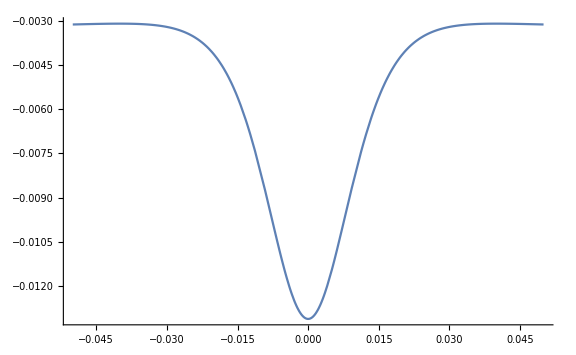

```mathematica
Plot[((Ufield[x, 0,-0.02,  0, 0, 0, 0, 2.07, 0.19 ]-M g 0.02) /. Abs->RemoveAbs//FullSimplify), {x, -0.05,0.05}]
```

```mathematica
Manipulate[
Plot[
{((Ufield[x, 0,z,  0, 0, 0, 0, 2.07, 0.19 ]+M g z) /. Abs->RemoveAbs//FullSimplify), ((Ufield[x, 0,z,  0, 0, 0, 30 Degree, 2.07, 0.19 ]+M g z) /. Abs->RemoveAbs//FullSimplify), ((Ufield[x, 0,z,  0, 0, 0, -30 Degree, 2.07, 0.19 ]+M g z) /. Abs->RemoveAbs//FullSimplify)}, {z, 0,-0.1}, PlotRange->{All;{-0.05, 0}}],
{{x,-0.02}, 0, -0.05}
]
```

```mathematica
Plot[((Ufield[0.01, 0,z,  0, 0, 0, 0, 2.07, 0.19 ]+M g z) /. Abs->RemoveAbs//FullSimplify), {z, 0,-0.05}]
```

```mathematica
Manipulate[
Plot3D[
((Ufield[x, y,z,  t, 0, 0, 0, 2.07, 0.19 ]+M g z-M ω^2 x^2/2) /. Abs->RemoveAbs//FullSimplify),
{x, -0.03, 0.03}, {z, -0.03, 0.03}, ColorFunction->"GrayYellowTones",PlotLegends->BarLegend[{Automatic,{-0.1, 0.1}}, 60], PlotRange->{{-0.03, 0.03},{-0.03, 0.03}, {-0.1, 0.1}}, AxesLabel->{"X", "Z", "U"}
], {ω, 0, 500}, {t, 0, 10}, {y, -0.03, 0.03}
]
```

```mathematica
Table[{FindMinimum[(Ufield[x, y,z,  0, -(90-24.5)/180 Pi+Pi, 0, 0, 2.07, 0.19 ]+M g 0.005) /. Abs->RemoveAbs//FullSimplify, {{x, -0.02}, {y, 0}}][[2, 1, 2]], z}, {z, 0, -0.05, -0.005}]
```

```mathematica
Show[
ListPlot[
Table[
{
((Ufield[x, 0,z,  0, -(90-24.5)/180 Pi+Pi, 0, 0, 2.07, 0.19 ]+M g z) /. Abs->RemoveAbs//FullSimplify)/.(FindMinimum[
(Ufield[x, y,z,  0, -(90-24.5)/180 Pi+Pi, 0, 0, 2.07, 0.19 ]+M g z) /. Abs->RemoveAbs//FullSimplify, {{x, -0.02}, {y, 0}}])
[[2, 1]], z}, {z, 0, -0.05, -0.005}],Frame->True, FrameLabel->{"энергия", "ось Z"}]]
```

FindMinimum::sdprec: Line search unable to find a sufficient decrease in the function value with MachinePrecision digit precision.

-Graphics-

```mathematica
Show[ListPlot[Table[{((Ufield[x, 0,z,  0, -(90-24.5)/180 Pi+Pi, 0, 0, 2.07, 0.19 ]+M g 0.005) /. Abs->RemoveAbs//FullSimplify), z}, {z, 0, -0.05, -0.005}],Frame->True, FrameLabel->{"Энергния", "ось Z"}], PlotRange->All]
```

-Graphics-

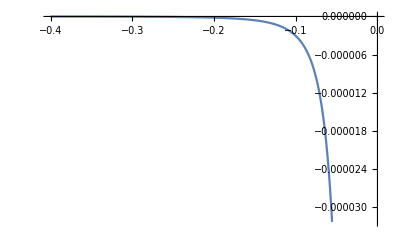

```mathematica
Plot[((Ufield[x, y,z,  0, -(90-24.5)/180 Pi+Pi, 0, 0, 2.07, 0.19 ]) /. Abs->RemoveAbs//FullSimplify)/.ParamOfPWell, {z, 0, -0.4}]
```

## Torque

```mathematica
Torque[x_, y_,z_, θ1_, ϕ1_, θ2_, ϕ2_,  p1_, p2_]:=m2[θ2,ϕ2, p2 ]*Field[x, y,z, θ1, ϕ1, p1]/. Abs->RemoveAbs//FullSimplify
```

```mathematica
Torque[x, y,z,  0, 30 Degree, a, ϕ, 2.07, 0.19 ]
```

{((3.933×10^-8 x^2-1.9665×10^-8 y^2+1.02182×10^-7 x z-1.9665×10^-8 z^2) Cos[a] Sin[ϕ])/((x^2+y^2+z^2)^(5/2)),(y (5.8995×10^-8 x+1.02182×10^-7 z) Sin[a] Sin[ϕ])/((x^2+y^2+z^2)^(5/2)),((-3.40608×10^-8 x^2-3.40608×10^-8 y^2+5.8995×10^-8 x z+6.81216×10^-8 z^2) Cos[ϕ])/((x^2+y^2+z^2)^(5/2))}

```mathematica
Manipulate[
Plot3D[
((Torque[x, y,z,  0, -(90-24.5)/180 Pi+Pi, t, ϕ, 2.07, 0.19 ][[1]]) /. Abs->RemoveAbs//FullSimplify),
{x, -0.03, 0.03}, {y, -0.03, 0.03}, ColorFunction->"GrayYellowTones",PlotLegends->BarLegend[{Automatic,{-0.1, 0.1}}, 60], PlotRange->{{-0.03, 0.03},{-0.03, 0.03}, {-0.1, 0.1}}, AxesLabel->{"X", "Z", "U"}
], {ω, 0, 500}, {t, 0, 2Pi}, {z, -0.03, 0.03}, {ϕ, 0, 2Pi}
]
```

## Experimental part

### Dipole moment

```mathematica
FieldDist=Import["/Users/kuleshovladimir/Desktop/Problems/2023/IPT/16. Unstable levitation/Experiments.xlsx",{"Data", 1, Table[i, {i, 9,69}], {5, 2}}];
(*FieldDist[[;;, 1]]=(2 μ0)/(4 Pi)(FieldDist[[;;, 1]] 10^-3)^-3;
FieldDist[[;;, 2]]=FieldDist[[;;, 2]] 10^-3;*)
```

```mathematica
FieldDist[[1;;16]]
```

{{2.5,400.},{10.5,42.},{21.5,7.},{6.5,149.},{3.5,316.},{5.5,220.},{4.5,286.},{7.5,125.},{8.5,102.},{9.5,75.},{12.5,35.},{11.5,45.},{14.5,26.2},{16.5,15.1},{19.5,9.5},{17.5,13.65}}

```mathematica
nlm1=NonlinearModelFit[FieldDist[[1;;24-8]], a Exp[b x], {a, b, c, d}, x];
```

```mathematica
Manipulate[
Show[
ListPlot[Table[{Around[FieldDist[[i, 1]], 1], FieldDist[[i, 2]]},{i, 24-8}]],
 Plot[a/x^3, {x, 0, 20}, PlotStyle->Orange],
 Plot[nlm1[x], {x, 0, 20},PlotStyle->Darker[Green]],
 AspectRatio->0.5, AxesStyle->Black, AxesOrigin->{0, 0}, PlotRange->{{0, 20}, {0, 450}}, BaseStyle->FontSize->15
],{{a, 74000}, 0, 10^6}, {{b, 74000}, 0, 10^6}
]
```

Part::partd: Part specification FieldDist⟦1,1⟧ is longer than depth of object.

Part::partd: Part specification FieldDist⟦1,2⟧ is longer than depth of object.

Part::partd: Part specification FieldDist⟦2,1⟧ is longer than depth of object.

General::stop: Further output of Part::partd will be suppressed during this calculation.

```mathematica
(24.5/10.7)^-1
```

0.436735

```mathematica
FieldDistGetaClass={{1.75,1260.},{1.85,1026.67},{2.06,820.},{2.22,673.33},{2.38,540.},{2.5300000000000002,433.33},{2.84,320.},{3.27,200.},{3.59,140.},{4.0200000000000005,113.33},{4.41,73.33},{4.82,60.},{5.3100000000000005,46.67},{5.64,46.67},{6.08,33.33},{6.44,33.33},{6.84,26.67},{7.26,26.67},{7.66,26.67},{8.120000000000001,13.33},{8.56,13.33},{8.870000000000001,20.},{9.43,13.33},{9.790000000000001,13.33},{10.370000000000001,13.33},{10.73,13.33},{11.21,2},{11.51,13.33},{12.01,2}};
```

```mathematica
Manipulate[
Show[
ListPlot[FieldDistGetaClass], 
Plot[a/x^3, {x, 0, 15}, PlotStyle->Orange], 
Plot[7377.97/x^3, {x, 0, 15},PlotStyle->Darker[Green]],
 AspectRatio->0.5, AxesStyle->Black, AxesOrigin->{0, 0}, PlotRange->{{0, 20}, {0, 450}}, BaseStyle->FontSize->15], {{a, 44000}, 0, 10^6}, {{b, 44000}, 0, 10^6}, {{n, 3}, 1, 5}]
```

ListPlot::lpn: FieldDistGetaClass is not a list of numbers or pairs of numbers.

Show::gcomb: Could not combine the graphics objects in Show[ListPlot[FieldDistGetaClass],,,AspectRatio→0.5,AxesStyle→color,AxesOrigin→{0,0},PlotRange→{{0,20},{0,450}},BaseStyle→FontSize→15].

ListPlot::lpn: FieldDistGetaClass is not a list of numbers or pairs of numbers.

Show::gcomb: Could not combine the graphics objects in Show[ListPlot[FieldDistGetaClass],,,AspectRatio→0.5,AxesStyle→color,AxesOrigin→{0,0},PlotRange→{{0,20},{0,450}},BaseStyle→FontSize→15].

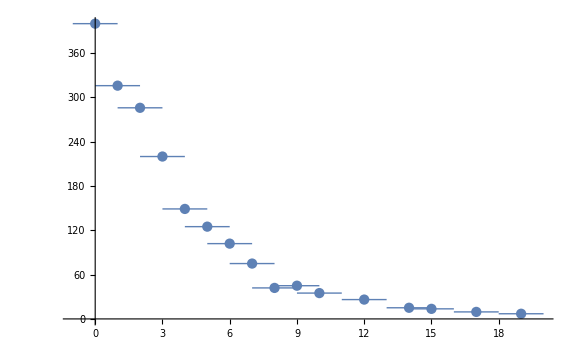

```mathematica
ListPlot[Table[{Around[FieldDist[[i, 1]], 1], FieldDist[[i, 2]]},{i, 24-8}]]
```

```mathematica
(*1-16 (9-24) cylinder base, 17-29 (28-40) side cylinder, 30-34 (43-47) squre, 35-42 (62-69) cube*)
```

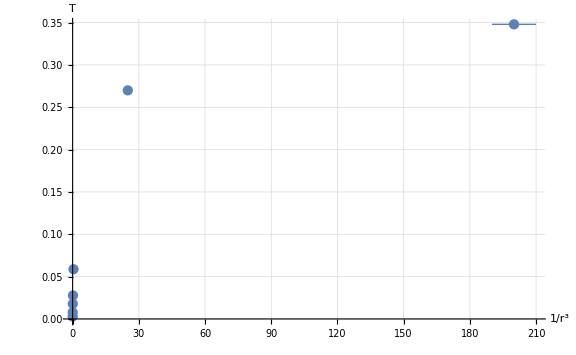

```mathematica
ListPlot[Table[{Around[FieldDist[[i]][[1]], FieldDist[[i]][[1]] 0.05] , FieldDist[[i]][[2]]}, {i,54, 61 }], PlotRange->All, GridLines->Automatic, AxesLabel->{"1/r^3", "T"}]
```

```mathematica
nlm[first0_, last0_]:=Module[{first=first0, last=last0,nl}, nl=NonlinearModelFit[Table[{FieldDist[[i]][[1]] , FieldDist[[i]][[2]]}, {i,first, last }], k x, {k},x];
Return[nl]]
```

```mathematica
Evaluate[nlm[58, 61][x]]
```

0.19491 x

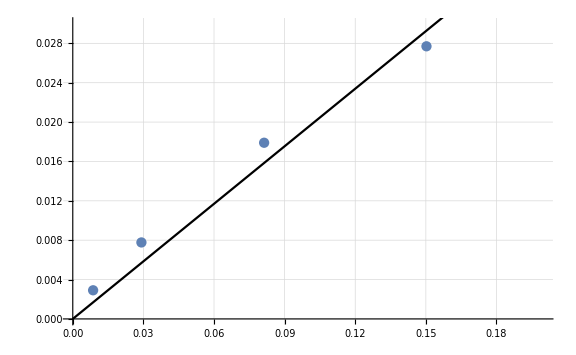

```mathematica
Show[ListPlot[Table[{FieldDist[[i]][[1]] ,FieldDist[[i]][[2]]}, {i,55, 61 }]], Plot[Evaluate[nlm[58, 61][x]], {x, 0,0.2}, PlotStyle->Black],PlotRange->{{0, 0.2}, {0, 0.03}}, GridLines->Automatic, , AxesLabel->{"1/r^3", "T"}]
```

```mathematica
dipoleMoments={cubic->0.19, sphere->2.07};
```

### Investigation of oscillations

```mathematica
imp1=Import["/Users/kuleshovladimir/Desktop/Problems/2023/IPT/16. Unstable levitation/Experiments.xlsx",{"Data", 3, Table[i, {i, 3,199}], {14, 15, 19, 20, 16, 17, 1, 11, 12}}];
```

```mathematica
Manipulate[Graphics3D[{{Red, Arrow[{{0, 0, 0}, {imp1[[i]][[1]], imp1[[i]][[3]], imp1[[i]][[2]]+imp1[[i]][[4]]}}]}}, PlotRange->{{-0.015, 0.015}, {-0.015, 0.015},{-0.015, 0.03}},Axes->True], {i, 1, Length[imp1], 1}]
```

```mathematica
imp1[[ Length[imp1]]][[7]]
```

39.2

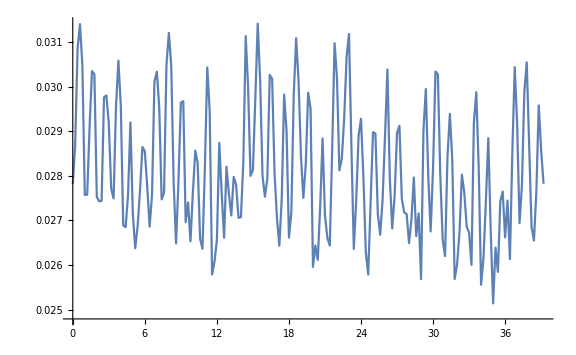

```mathematica
ListLinePlot[Table[{imp1[[i]][[7]], imp1[[i]][[2]]+imp1[[i]][[4]]}, {i, Length[imp1]}]]
```

```mathematica
Mean[Table[ imp1[[i]][[2]]+imp1[[i]][[4]], {i, Length[imp1]}]]
```

0.0281376

```mathematica
imp1[[76]][[8]]
```

6.56

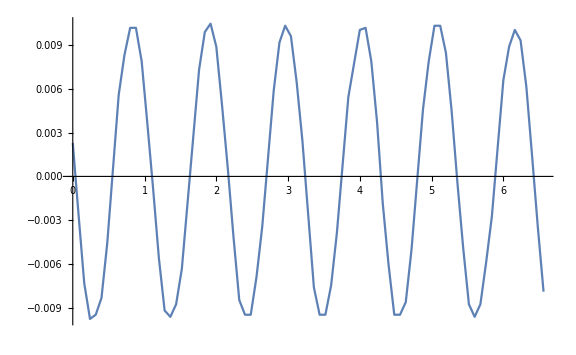

```mathematica
ListLinePlot[Table[{imp1[[i]][[8]], imp1[[i]][[9]]}, {i,76}]]
```

```mathematica
Mean[Table[Abs[imp1[[i]][[3]]-0.0005299249], {i, 1, 197}]]
```

0.00047514

```mathematica
Mean[Table[Abs[imp1[[i]][[1]]], {i, 1, 197}]]
```

0.0022356

```mathematica
Table[ListLinePlot[Table[{imp1[[i]][[1]], (imp1[[i]][[3]]-0.0005299249)*0.0022355/0.000475}, {i, j, 10+j}], PlotRange->{{-0.006, 0.006}, {-0.006, 0.006}}], {j, 1, 187, 1}];
```

```mathematica
(*Export["/Users/kuleshovladimir/Desktop/Problems/2023/IPT/16. Unstable levitation/Videos/XY motion.mp4", %36];*)
```

```mathematica
N[ArcTan[1/5]]
```

0.197396

```mathematica
180/Pi 0.19
```

10.8862

```mathematica
Manipulate[ParametricPlot[{Cos[t]+0.5Cos[ν t],Sin[t]+0.5Sin[ν t]},{t, 0, 2Pi}, PlotRange->{{-3, 3}, {-3, 3}}], {ν, 0, 10, 1}]
```

```mathematica
FFT[data0_]:=Module[{data=data0, fdata, ft}, 
fdata=Abs@Fourier[data[[All,2]]];
ft={#/(Length[fdata]-1),fdata[[#+1]]}&/@Range[0,Length[fdata]-1];
Return@fdata]
```

```mathematica
MeanFilter
```

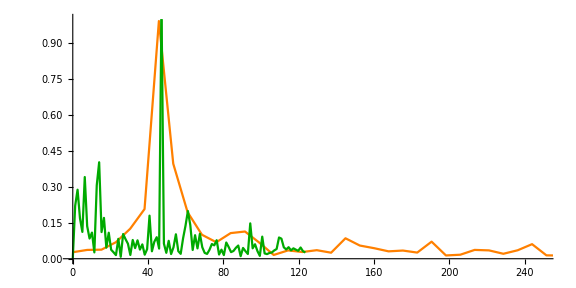

```mathematica
ListLinePlot[{Table[{(j-1)/6.56 50, FFT[Table[{imp1[[i]][[8]], (imp1[[i]][[9]])/0.04}, {i, 76}]][[j]]}, {j, Length[ FFT[Table[{imp1[[i]][[8]], imp1[[i]][[9]]}, {i, 76/2}]]]}],Table[{(j-1)/39.26 50,FFT[Table[{imp1[[i]][[7]], (imp1[[i]][[2]]+imp1[[i]][[4]]-0.028137)/0.01}, {i,197}]][[j]]}, {j, Length[FFT[Table[{imp1[[i]][[7]], imp1[[i]][[2]]+imp1[[i]][[4]]}, {i,197/2}]]]}]}, PlotRange->{{0, 5 50}, {0,1}}, ImageSize->Large, AspectRatio->1/2,  PlotStyle->{Orange, Darker[Green]} ]
```

```mathematica
(24 0.19^2)/0.016 1/0.023^5
```

8.41316×10^9

```mathematica
impVideo=Import["/Users/kuleshovladimir/Desktop/Problems/2023/IPT/16. Unstable levitation/Videos/anton222.avi",{"MP4","ImageList",Range[1,950,5]}];
```

```mathematica
imagecut=Table[ImageTake[impVideo[[i]], {233, 525}, {375, 635}],{i, Length[impVideo]}];
```

```mathematica
imagecut[[24]]
```

-Graphics-

```mathematica
Table[Show[imagecut[[i]], Graphics[{{Red,Arrowheads[0.05],Thickness[0.01], Arrow[{{134 +3423imp1[[i]][[5]], 115+3423imp1[[i]][[6]]}, {134+3423imp1[[i]][[1]]+3423imp1[[i]][[5]],115+3423 imp1[[i]][[2]]+3423imp1[[i]][[4]]+3423imp1[[i]][[6]]}}]}}, PlotRange->{{-0.015, 0.015}, {-0.015, 0.015}},Axes->True], Axes->True],  {i, 1, 190, 1}];
```

```mathematica
(*Export["/Users/kuleshovladimir/Desktop/Problems/2023/IPT/16. Unstable levitation/Videos/dipole_moment.mp4", %68];*)
```

### Distance to magnet

```mathematica
imp2=Import["/Users/kuleshovladimir/Desktop/Problems/2023/IPT/16. Unstable levitation/Experiments.xlsx", {"Data", 4, All, {3, 2}}]
```

{{масса,период (500 кадров)},{15.489,22.25},{18.682,23.5},{21.66,24.5},{24.744,24.75},{27.77,25.25},{30.874,25.},{,},{12.463,14.6667},{9.362,14.75},{,большой},{масса,период (500 кадров)},{31.557,25.1429},{34.587,25.8571},{21.963,23.9048},{18.87,23.6364},{21.972,23.5652},{25.002,25.619},{28.442,25.3636},{12.263,20.381},{,},{,},{,маленький},{масса,период (500 кадров)},{19.374,21.1},{13.243,22.7826},{7.059,21.8182},{10.079,21.6364},{16.271,21.3636},{23.009,21.4},{26.118,21.44},{,},{,расстояние до магнита},{масса,расстояние},{19.374,6.1},{13.243,11.},{7.059,9.7},{10.079,7.2},{16.271,7.4},{23.009,5.7},{26.118,4.6},{12.263,19.34},{31.557,13.89},{34.587,14.08},{21.963,15.57},{18.87,15.96},{21.972,16.26},{25.002,15.41},{28.442,14.56}}

```mathematica
Clear[nlm, nlm1]
```

```mathematica
Table[{Around[(imp2[[i]][[1]])/2, 0.1], Around[imp2[[i]][[2]], 0.1]}, {i, 2, 9}]
```

{{7.740.10,22.250.10},{9.340.10,23.500.10},{10.830.10,24.500.10},{12.370.10,24.750.10},{13.890.10,25.250.10},{15.440.10,25.000.10},{/20.10,0.10},{6.230.10,14.670.10}}

```mathematica
Table[{imp2[[i]][[1]],imp2[[i]][[2]]}, {i, 35, 41}]
```

```mathematica
nlm=NonlinearModelFit[Join[Table[{imp2[[i]][[1]],imp2[[i]][[2]]}, {i, 35, 41}]],a x^n, {a, n, d}, x]
nlm1=NonlinearModelFit[Join[Table[{imp2[[i]][[1]],imp2[[i]][[2]]}, {i, 42, 49}]],a x^n, {a, n, d}, x]
```

FittedModel[23.6314/x^0.434539]

FittedModel[42.2857/x^0.31763]

```mathematica
nlm3=NonlinearModelFit[Join[Table[{imp2[[i]][[1]],imp2[[i]][[2]] 24/1000}, {i, 2, 7}]],a x^n, {a, n, d}, x]
```

FittedModel[0.340222 x^0.171401]

```mathematica
Manipulate[Plot[(2 Pi)/(√((1.0664-79.39 r)/(m r))), {m,0, 0.03}], {r, 0.0001, 0.01}]
```

```mathematica
Table[{Around[imp2[[i]][[1]], 0.1], Around[imp2[[i]][[2]] 24/1000, 5/1000]}, {i, 2, 7}]
```

{{15.490.10,0.5340.005},{18.680.10,0.5640.005},{21.660.10,0.5880.005},{24.740.10,0.5940.005},{27.770.10,0.6060.005},{30.870.10,0.6000.005}}

```mathematica
Manipulate[
Show[
ListPlot[
{
Table[{Around[imp2[[i]][[1]], 0.1], Around[(imp2[[i]][[2]])/1 24/1000, 5/1000]}, {i, 2, 7}],
Table[{Around[imp2[[i]][[1]], 0.1], Around[imp2[[i]][[2]] 24/1000, 5/1000]}, {i, 13, 20}]
}
],
Plot[(2 Pi)/(√(a(1.0664-79.39 r)/(0.001m r))), {m,0, 35}], 
Plot[0.34 m^0.17, {m,0.001, 35}], 
PlotRange->{{-1, 35}, {0, 0.8}}, AxesOrigin->{0, 0}
], {{r,0.01306} , 0.0001, 0.0138}, {a, 0.0001, 100}
]
```

Part::partd: Part specification imp2⟦2⟧ is longer than depth of object.

Part::partd: Part specification imp2⟦3⟧ is longer than depth of object.

General::stop: Further output of Part::partd will be suppressed during this calculation.

Part::partd: Part specification imp2⟦2⟧ is longer than depth of object.

Part::partd: Part specification imp2⟦3⟧ is longer than depth of object.

General::stop: Further output of Part::partd will be suppressed during this calculation.

Part::partd: Part specification imp2⟦2⟧ is longer than depth of object.

Part::partd: Part specification imp2⟦3⟧ is longer than depth of object.

General::stop: Further output of Part::partd will be suppressed during this calculation.

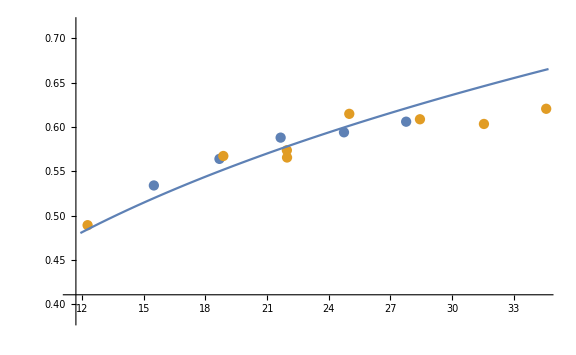

```mathematica
Show[
ListPlot[
{
Table[{Around[imp2[[i]][[1]], 0.1], Around[imp2[[i]][[2]] , 5/1000]}, {i, 35, 41}],
Table[{Around[imp2[[i]][[1]], 0.1], Around[imp2[[i]][[2]], 5/1000]}, {i, 42, 49}]
}
],
Plot[{nlm[x],nlm1[x]}, {x,7, 35}, PlotStyle->Black],
PlotRange->All
]
```

```mathematica
Manipulate[
Graphics3D[{
{Cylinder[{{Cos[t](0.5+Cos[t+Pi/2]/2), Sin[t](0.5+Cos[t+Pi/2]/2), 0}, {Cos[t](0.5+Cos[t]/2), Sin[t](0.5+Cos[t]/2), 1}}, 0.5]}
},
PlotRange->{{-2, 2}, {-2, 2}, {-0.5, 1.5}}, Boxed->False],
{t, 0, 2Pi}
]
```

```mathematica
Export["/Users/kuleshovladimir/Desktop/Problems/2023/IPT/16. Unstable levitation/Videos/cylinder.mp4", %101]
```

/Users/kuleshovladimir/Desktop/Problems/2023/IPT/16. Unstable levitation/Videos/cylinder.mp4